```mathematica
<<"ACPackages`"
<<"ErrorBarPlots`"
```

```mathematica
$WD=NotebookDirectory[];
```

Table of results: 
list of {
	independent:
date(year,month,day), mesh(Nx=Nz,Ny), TDV(type of time-dependance of velocity,0=const,1=perm), ADV(approximation of velocity,0=default),ksi,chi(for v),κ=r/R,length along channel(lfi),width of wall,Rvac, eta of wall,Rm,
	dependent:
m(in section),n(along channel),gamma,δgamma,omega,δomega,comment("kalibr+BC")
}

```mathematica
indepkol = 16;
depkol = 5;
```

```mathematica
Было:{"year","month","day","TDV","ADV","ksi","r/R","Rm","k","gamma","δgamma","omega","δomega","kalibr+BC"}
```

## Формирование записей

```mathematica
SetDirectory["D:\\Работа\\Programs\\tormagn\\2008-01-07"]
```

```mathematica
SetWorkDir["2008-01-07"]
```

D:\Работа\Programs\tormagn\2008-01-07

```mathematica
(*putlist=Join[Take[Date[],3],{Nxz,Ny,TDV=0,ADV=0,ksi=18,chi=1,1/5,lfi=2π,wall,ηwall=1,Rm=10,m,n,gamma,0.143,omega,0.85,"etafl+norm"}]*)
putlist={2015,10,2,32,32,TDV=0,ADV=0,ksi=0,chi=1.1,r=0.25,lfi=(2π)/0.701,wall=0,Rvac=2,ηwall=1,Rm=141.7954,m=1,n=1,γ=0.,0.001,8.890,0.001,"homogen"}
```

{2015,10,2,32,32,0,0,0,1.1,0.25,8.96317,0,2,1,141.795,1,1,0.,0.001,8.89,0.001,homogen}

```mathematica
putlist>>>$WD<>"Dean.dat"
Clear[TDV,ADV,ksi,chi,r,lfi,wall,Rvac,ηwall,Rm,m,n,γ,ω]
```

```mathematica
putlist>>>$WD<>"result.dat"
Clear[TDV,ADV,ksi,chi,r,lfi,wall,Rvac,ηwall,Rm,m,n,γ,ω]
```

```mathematica
2π/0.92
```

## Анализ записей

### Функции

```mathematica
UpdateData:=Block[{},Print[fields=Module[{res,stm},res=ReadList[stm=StringToStream[First[ReadList[$WD<>"\\result.dat"]]],Word,WordSeparators->{" ",",","{","}"}];Close[stm];res]];
all=Select[Rest[ReadList[$WD<>"\\result.dat"]]/.{a_+b_ E->b*10^a}/.{a_+b_ e->b*10^a},StringFreeQ[Last[#],"wrong"]&];
Print["Total:",Length[all]," records"];]
```

```mathematica
UpdateDataDean:=Block[{},Print[fields=Module[{res,stm},res=ReadList[stm=StringToStream[First[ReadList[$WD<>"\\Dean.dat"]]],Word,WordSeparators->{" ",",","{","}"}];Close[stm];res]];
all=Select[Rest[ReadList[$WD<>"\\Dean.dat"]]/.{a_+b_ E->b*10^a}/.{a_+b_ e->b*10^a},StringFreeQ[Last[#],"wrong"]&];
Print["Total:",Length[all]," records"];]
```

```mathematica
MakeRule[el_]:=MapThread[Rule,{fields,el}];
```

```mathematica
ShowDependance[param_,conditions_:{}]:=Block[{allbut=GetResults[conditions],dep,indep,numpar,othern,otherv},If[FreeQ[Drop[fields,{indepkol+1,-2}],param],Print["Wrong parameter"];Return[]];numpar=First[Flatten[Position[fields,param]]];othern=Complement[Join[Range[4,Length[fields]-depkol-1],{Length[fields]}],{numpar}];
Print[othern];
Print["All such parameters=",Union[(#1⟦numpar⟧&)/@allbut]];dep=First[Rest[Reap[(Sow[#1,NotList@@#1⟦othern⟧]&)/@Sort[allbut,N[#1⟦numpar⟧]<N[#2⟦numpar⟧]&],_,f]]];dep=Select[dep,Length[Last[#1]]>1&];otherv=Drop[Drop[Drop[fields,{indepkol+1,-2}],{numpar}],3];Print[otherv];nom=0;If[Length[dep]==0,Print["Data was not found"];Return[]];Print["Plots can be shown for parameters:"];(Print["№",++nom,":",MapThread[Rule,{otherv,List@@First[#1]}],", number of points=",Length[Last[#1]]]&)/@dep;If[Length[dep]>1,nom=Input["Введите номер желаемой зависимости"],nom=1];Print["So constant parameters are:"];Print["\t",Thread[otherv->List@@First[dep⟦nom⟧]]];pts={param,"gamma","δgamma","omega","δomega","kalibr+BC"}/.MakeRule/@Last[dep⟦nom⟧];If[param≠Last[fields],Print[{ErrorListPlot[{({{#1⟦1⟧,#1⟦2⟧},ErrorBar[#1⟦3⟧]}&)/@pts},AxesLabel->{param,"gamma"},Axes->True,Frame->False,PlotRange->All,PlotMarkers->{●}],ErrorListPlot[{({{#1⟦1⟧,#1⟦4⟧},ErrorBar[#1⟦5⟧]}&)/@pts},AxesLabel->{param,"omega"},Axes->True,Frame->False,PlotRange->All,PlotMarkers->{■}]}]];ErrorListPlot[{({{#1⟦2⟧,#1⟦4⟧},ErrorBar[#1⟦3⟧,#1⟦5⟧]}&)/@pts},AxesLabel->{"gamma","omega"},Axes->True,Frame->False,PlotRange->All,PlotMarkers->{◆}]];
```

```mathematica
GetResults[conditions_:{}]:=Block[{pattern,rules=Union[Select[conditions,Head[#]==Rule&]],
(*Unequal doesn't work always*)
ineqs=And@@Flatten[Select[conditions,MemberQ[{Less,LessEqual,Greater,GreaterEqual,Unequal},Head[#]]∨#==False&]]},
MatchesQ[el_]:=Module[{mr=MakeRule[el]},Simplify[ineqs/.mr]∧Complement[rules,mr]=={}];
Print["All data matches (",Simplify[ineqs],")",Sequence@@("&&("<>First[#]<>"="<>ToString[InputForm[Last[#]]]<>")"&/@rules),":"];
Return[Select[all,MatchesQ]];
];
```

### Действия

```mathematica
UpdateData
```

{year,month,day,Nxz,Ny,TDV,Re,ksi,chi,r/R,lfi,wall,Rvac,etawall,Rm,m,n,gamma,δgamma,omega,δomega,kalibr+BC}

Total:1167 records

```mathematica
UpdateDataDean
```

{year,month,day,Nxz,Ny,TDV,Re,ksi,chi,r/R,lfi,wall,Rvac,etawall,Rm,m,n,gamma,δgamma,omega,δomega,kalibr+BC}

Total:503 records

```mathematica
GetResults[{"r/R">0.05,"chi"->0.7692307692307692,"wall"->0,"Nxz">60,"Nxz"<250,"Rm"<100}]
```

```mathematica
GetField[#,"gamma"]&/@GetResults[{"Rm"->15}]
```

All data matches (True)&&(Rm=15):

{-0.518,-0.228926,-0.0499241,0.0201533,-0.0174837,-0.860808,-1.26989,-0.146791,-0.0100901,0.0180088,0.0211816}

```mathematica
$res=GetResults[{}];Length[$res]
```

All data matches (True):

196

```mathematica
$res=GetResults[{"r/R"->0.78,"chi"->0.5,"etawall">0}];
```

All data matches (etawall>0)&&(chi=0.5)&&(r/R=0.78):

```mathematica
GetResults[{"ksi"≠∞}]
```

All data matches (ksi≠∞):

{{2006,2,16,64,32,0,0,18,1,0,2 π,0.3,2,0.2,20,?,?,-0.155,0.005,3.5,0.45,etafl+norm},{2006,2,16,64,32,0,0,18,1,0,2 π,0.3,2,0.2,30,?,?,0.522,0.003,4.56,0.22,etafl+norm},{2006,2,19,64,32,0,0,18,1,1/4,2 π,0.3,2,0.2,10,?,?,-0.96,0.2,3,0.75,etafl+norm},{2006,2,19,64,32,0,0,18,1,1/4,2 π,0.3,2,0.2,20,?,?,-0.31,0.2,2.17,0.75,etafl+norm},{2006,2,20,64,32,0,0,18,1,1/4,(8 π)/3,0.3,2,0.2,10,?,?,-0.52,0.177,0.7,0.5,etafl+norm},{2006,2,21,64,32,0,0,18,1,0.3,(20 π)/9,0.333,2.5,0.2,20,?,?,0.08,0.15,3.5,1.2,etafl+norm},{2006,2,21,64,32,0,0,18,1,0.3,(20 π)/9,0.333,2.5,0.2,30,?,?,0.69,0.008,3.46,0.18,etafl+norm},{2006,3,7,60,30,0,0,18,1,1/4,2 π,0.3,2.5,0.2,10,?,?,-1.05,0.5,3,2,etafl+norm},{2006,3,7,60,30,0,0,18,1,1/4,2 π,0.3,2.5,0.2,20,?,?,-0.26,0.1,2.7,0.4,etafl+norm},{2006,3,7,60,30,0,0,18,1,1/4,2 π,0.3,2.5,0.2,30,?,?,0.399,0.0035,4.91,0.42,etafl+norm},{2006,3,7,60,30,0,0,18,1,1/4,2 π,0.3,2.5,0.2,40,?,?,1.018,0.0045,5.89,0.17,etafl+norm},{2006,3,7,60,30,0,0,18,1,1/4,2 π,0.3,2.5,0.2,40,?,?,1.24,0.01,6.18,0.22,etavac+norm},{2006,3,14,64,32,0,0,18,1,1/10,2 π,0.3,2.5,0.2,30,?,?,0.544663,0.0008,4.85,0.12,etafl+norm},{2006,3,14,64,32,0,0,18,1,1/7,2 π,0.3,2.5,0.2,10,?,?,-0.93,0.04,2.15,0.23,etafl+norm},{2006,3,14,64,32,0,0,18,1,1/6,2 π,0.3,2.5,0.2,10,?,?,-0.9,0.08,2.04,0.2,etafl+norm},{2006,3,14,64,32,0,0,18,1,1/5,2 π,0.3,2.5,0.2,10,?,?,-0.94,0.143,1.75,0.85,etafl+norm},{2006,3,20,64,32,0,0,18,1,1/5,2 π,0.3,2.5,0.2,20,?,?,-0.172,0.018,3.51,0.1,etafl+norm},{2006,3,20,64,32,0,0,18,1,1/6,2 π,0.3,2.5,0.2,20,?,?,-0.158,0.015,3.64,0.12,etafl+norm},{2006,3,20,64,32,0,0,18,1,1/7,2 π,0.3,2.5,0.2,30,?,?,0.4805,0.0015,4.72,0.16,etafl+norm},{2006,3,20,64,32,0,0,18,1,1/10,2 π,0.3,2.5,0.2,20,?,?,-0.1308,0.0006,3.69,0.13,etafl+norm},{2006,3,21,64,32,0,0,18,1,1/10,2 π,0.3,2.5,0.2,10,?,?,-0.888,0.005,2.22,0.12,etafl+norm},{2006,3,21,64,32,0,0,18,1,1/5,2 π,0.3,2.5,0.2,30,?,?,0.487,0.0008,4.9,0.14,etafl+norm},{2006,3,24,64,32,0,0,18,1,1/7,2 π,0.3,2.5,0.2,20,?,?,-0.1972,0.0004,3.66,0.1,etafl+norm},{2006,3,24,64,32,0,0,18,1,1/6,2 π,0.3,2.5,0.2,30,?,?,0.5105,0.001,4.93,0.12,etafl+norm},{2007,8,10,64,32,0,0,0,1,0,6.28319,0.3,2,0.2,100,1,1,4.04709,0.001,12.1,0.4,},{2007,8,11,64,32,0,0,0,1,0.3,6.28319,0.3,2,0.2,100,1,1,3.89273,0.001,12.2,0.1,},{2007,8,12,64,32,1,0,0,1,0.3,6.28319,0.3,2,0.2,100,1,1,3.60525,-5.2,15,-10,}}

```mathematica
$res=GetResults[{"Nxz">20,"lfi">0,"chi"->1,"TDV"->0,"ksi"->∞,"wall"->0,"r/R">=0}];Length[$res]
```

All data matches (Nxz>20&&lfi>0&&r/R≥0)&&(chi=1)&&(ksi=Infinity)&&(TDV=0)&&(wall=0):

227

```mathematica
ShowTable[$res,{"Rm","gamma","omega","chi","lfi","n"}]
```

Rm | gamma | omega | chi | lfi | n
16 | 0.045 | 0.6 | 1.3 | 16.213 | 2
15 | 0.005 | 0.7 | 1.3 | 16.213 | 2
14 | -0.037 | 0.7 | 1.3 | 16.213 | 2
13 | -0.09 | 0.72138 | 1.3 | 16.213 | 2
12 | -0.14 | 0.62 | 1.3 | 16.213 | 2

```mathematica
Graphics3D[Point[#]&/@Union[GetFields[#,{"r/R","chi","Rm"}]&/@$res],AspectRatio->1,PlotRange->{{0.3,1},{0.4,1.6},{10,60}},Axes->True,
FaceGrids->All]
```

All data matches (True):

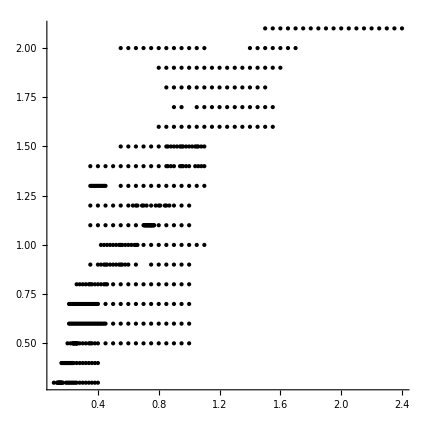

```mathematica
Graphics[Point[{2π/First[#],Last[#]}]&/@Union[GetFields[#,{"lfi","chi"}]&/@GetResults[{}]],AspectRatio->1,PlotRange->All,AxesOrigin->{0.,0.},Axes->True]
```

```mathematica
Sort[{2π#[[4]]/#[[1]],#[[2]],#[[3]],#[[4]]}&/@(GetFields[#,{"lfi","Rm","omega","m"}]&/@$res)]
```

{{0.19,350,2.6601,1},{0.195,304.973,2.85564,1},{0.2,289.837,3.094,1},{0.2,290.039,3.09594,1},{0.205,283.908,3.43,1},{0.21,282.557,3.6532,1},{0.215,284.06,3.9763,1},{0.22,287.466,4.3336,1},{0.22,287.478,4.3337,1},{0.225,292.109,4.72828,1},{0.23,297.351,5.1608,1},{0.235,302.708,5.6298,1},{0.24,307.812,6.13339,1},{0.24,314.9,6.48,1},{0.26,324.206,8.4391,1},{0.28,337.747,11.1811,1},{0.3,352.358,14.4077,1},{0.32,368.734,18.174,2},{0.32,368.739,18.175,1},{0.33,377.489,20.27,2},{0.34,386.56,22.515,2},{0.34,386.566,22.5183,1},{0.35,395.917,24.905,2},{0.36,405.542,27.46,2},{0.36,405.543,27.458,2},{0.36,405.549,27.4625,1},{0.37,415.95,30.2,2},{0.38,425.585,33.0355,1},{0.38,425.612,33.4,2},{0.4,446.678,39.2711,1}}

All data matches (gamma<δgamma&&gamma+δgamma>0&&5 lfi>m π)&&(chi=1.1):

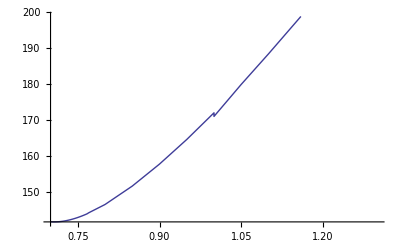

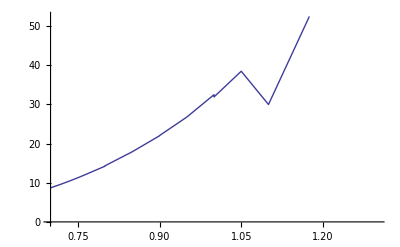

```mathematica
$res=GetResults[{"chi"->1.1,"gamma"<"δgamma","gamma">-"δgamma","lfi">2π"m"/10}];
(*$res=GetResults[{"chi"->2}];*)
ListLinePlot[Sort[{2π#[[3]]/#[[1]],#[[2]]}&/@(GetFields[#,{"lfi","Rm","m"}]&/@$res)]]
ListLinePlot[Sort[{2π#[[3]]/#[[1]],#[[2]]}&/@(GetFields[#,{"lfi","omega","m"}]&/@$res)]]
```

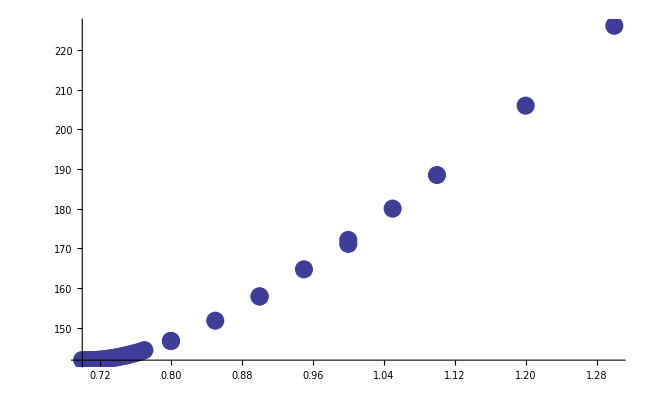

```mathematica
ListPlot[Sort[{2π#[[3]]/#[[1]],#[[2]]}&/@(GetFields[#,{"lfi","Rm","m"}]&/@$res)],PlotStyle->PointSize[0.02],PlotRange->All]
```

```mathematica
Export["d:\\DeanChi14.eps",%275,ImageResolution->300]
```

d:\DeanChi14.eps

```mathematica
GetResults[{"Nxz"->64,"Ny"->32,"TDV"->0,"ADV"->0,"ksi"->0,"chi"->1,"lfi"->2 π,"wall"->0.3,"Rvac"->2,"etawall"->0.2,"Rm"->100,"m"->1}]
```

All data matches (True)&&(ADV=0)&&(chi=1)&&(etawall=0.2)&&(ksi=0)&&(lfi=2*Pi)&&(m=1)&&(Nxz=64)&&(Ny=32)&&(Rm=100)&&(Rvac=2)&&(TDV=0)&&(wall=0.3):

{{2007,8,10,64,32,0,0,0,1,0,2 π,0.3,2,0.2,100,1,1,4.04709,0.001,12.1,0.4,},{2007,8,11,64,32,0,0,0,1,0.3,2 π,0.3,2,0.2,100,1,1,3.89273,0.001,12.2,0.1,}}

```mathematica
2π/0.77
```

8.15998

#### Все поля определённого типа

```mathematica
GetField[res_,field_String]:=Block[{num=Position[fields,field]},
If[Length[num]<1,Print["Field not found"];Return[$Failed]];
Extract[res,First[num]]
]
GetFields[res_,fs_List]:=GetField[res,#]&/@fs
ShowTable[fromres_,fs_List]:=Prepend[GetFields[#,fs]&/@fromres,fs]//TableForm
```

```mathematica
GetField[Union/@Transpose[$res],"etawall"]
```

{0}

```mathematica
GetField[Union/@Transpose[$res],"kalibr+BC"]
```

{etafl+norm,etavac+norm,etavac+zero,homogen}

```mathematica
MapThread[Join[{#1},#2]&,{fields,Union/@Transpose[$res]}]//TableForm
```

year | 2006 | 2007 | 2008 | 2009 | 2010 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
month | 1 | 2 | 3 | 4 | 6 | 7 | 8 | 9 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
day | 1 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 27 | 29 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Nxz | 20 | 30 | 32 | 60 | 64 | 128 | 256 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Ny | 20 | 30 | 32 | 64 | 176 | 200 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
TDV | 0 | 1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Re | 0 | 80 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
ksi | 0 | 18 | ∞ |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
chi | 0.5 | 0.7 | 0.769231 | 0.769231 | 0.8 | 0.85 | 0.9 | 0.9375 | 0.95 | 0.967188 | 0.979687 | 0.9875 | 0.996875 | 1 | 1.01875 | 1.03125 | 1.06094 | 1.1 | 1.12266 | 1.2 | 1.3 | 1.33 | 1.4 | 1.5 | 2 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
r/R | 0 | 0. | 0.05 | 0.1 | 1/10 | 0.14 | 1/7 | 0.15 | 0.161422 | 1/6 | 0.181818 | 0.2 | 1/5 | 0.23 | 0.25 | 1/4 | 0.3 | 0.325 | 0.35 | 0.35555 | 0.375 | 0.4 | 0.425 | 0.45 | 0.45555 | 0.46 | 0.475 | 0.48 | 0.5 | 1/2 | 0.52 | 0.525 | 0.54 | 0.55 | 0.55555 | 0.56 | 0.575 | 0.58 | 0.6 | 0.62 | 0.625 | 0.64 | 0.65 | 0.66 | 0.675 | 0.68 | 0.7 | 0.7091 | 0.72 | 0.725 | 0.74 | 0.75 | 0.759091 | 0.76 | 0.775 | 0.78 | 0.8 | 0.809091 | 0.825 | 0.85 | 0.859091 | 0.875 | 0.9 | 0.909091 | 0.925 | 0.95 | 0.975 | 1 | 1. |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
lfi | 3.5 | 5.23599 | 5.71199 | 6.28319 | 6.28319 | 6.28319 | 6.44429 | 6.61388 | 6.79263 | 6.9115 | 6.98132 | 6.98132 | 6.98132 | 7.18078 | 7.31376 | 7.39198 | 7.61598 | 7.76573 | 7.78479 | 7.85398 | 7.85398 | 7.85398 | 7.854 | 7.96245 | 7.98181 | 8.05537 | 8.10734 | 8.18013 | 8.26735 | 8.27715 | 8.27725 | 8.37758 | 8.37758 | 8.42409 | 8.43026 | 8.49079 | 8.63939 | 8.66646 | 8.72665 | 8.75705 | 8.97598 | 8.97598 | 8.97598 | 9.08139 | 9.10607 | 9.17253 | 9.23998 | 9.30842 | 9.49404 | 9.51322 | 9.51998 | 9.5211 | 9.529 | 9.66644 | 9.73099 | 9.81748 | 10.0531 | 10.1342 | 10.1662 | 10.1752 | 10.472 | 10.472 | 10.7405 | 10.7635 | 10.8331 | 10.9273 | 11.22 | 11.22 | 11.3098 | 11.424 | 11.5192 | 11.6355 | 11.968 | 12.083 | 12.5664 | 12.5664 | 12.5664 | 12.5664 | 12.5664 | 12.955 | 12.9747 | 13.09 | 13.2278 | 13.3685 | 13.6591 | 13.7925 | 13.9626 | 14 | 14.6975 | 14.784 | 15.708 | 15.708 | 16.213 | 16.7552 | 17.6717 | 17.952 | 19.3329 | 20.944 | 20.944 | 91.7253 | 2 π | (20 π)/9 | (8 π)/3 | 4 π |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
wall | 0 | 0.2 | 0.3 | 0.333 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Rvac | 2 | 2.5 | 3 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
etawall | 0 | 0.2 | 1 | 5 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Rm | 5 | 6 | 7.5 | 8.5 | 9 | 10 | 11 | 12 | 12.5 | 13 | 13.5 | 14 | 14. | 14.5 | 14.7 | 14.715 | 14.72 | 14.7379 | 14.7498 | 14.75 | 14.7603 | 14.7624 | 14.7951 | 14.7957 | 14.8 | 14.8969 | 14.9 | 14.9809 | 15 | 15.0195 | 15.0746 | 15.1161 | 15.1369 | 15.2 | 15.2511 | 15.3019 | 15.311 | 15.3385 | 15.3465 | 15.5 | 15.5171 | 15.547 | 15.6335 | 15.6352 | 15.6366 | 15.7871 | 16 | 16.0014 | 16.0372 | 16.0404 | 16.0856 | 16.2807 | 16.3089 | 16.5 | 16.5555 | 16.5715 | 16.6 | 16.6159 | 16.9936 | 17 | 17.0416 | 17.254 | 17.3732 | 17.44 | 17.5 | 17.54 | 17.6 | 17.66 | 18 | 18.0181 | 18.8 | 19 | 19. | 19.31 | 19.7 | 19.8095 | 19.839 | 19.866 | 19.89 | 19.9161 | 19.9256 | 19.9605 | 20 | 20. | 20.03 | 20.035 | 20.0391 | 20.05 | 20.0588 | 20.0615 | 20.14 | 20.145 | 20.17 | 20.19 | 20.1952 | 20.198 | 20.23 | 20.2765 | 20.2855 | 20.3 | 20.31 | 20.35 | 20.3521 | 20.3764 | 20.3798 | 20.4749 | 20.5455 | 20.6035 | 20.6962 | 20.7374 | 20.74 | 21 | 21.1392 | 21.3338 | 21.3727 | 21.4 | 21.4522 | 21.4817 | 21.4887 | 21.5 | 21.5698 | 21.6 | 21.63 | 21.6804 | 21.7 | 21.714 | 21.8093 | 21.9024 | 21.9089 | 21.9443 | 22 | 22.1443 | 22.2726 | 22.4012 | 22.5 | 22.6452 | 22.6499 | 22.8135 | 23 | 23.0449 | 23.212 | 23.3 | 23.5 | 23.5408 | 23.66 | 23.8008 | 24 | 24.55 | 24.9139 | 25 | 25.3 | 25.37 | 25.7 | 26 | 26.55 | 27 | 27.5 | 27.8 | 28 | 28.95 | 28.99 | 30 | 30.2 | 30.4 | 30.5 | 32 | 32.5 | 34 | 34.113 | 34.2 | 34.459 | 35 | 36 | 37.6689 | 38 | 39.67 | 40 | 40.3 | 40.8 | 41 | 41.2 | 41.5 | 41.6201 | 42 | 42.5 | 44 | 45 | 46 | 46.45 | 48 | 49.5 | 50 | 52 | 53.6975 | 53.7787 | 54 | 54.0187 | 54.3 | 54.4055 | 54.9204 | 55 | 55.5277 | 56 | 56.1905 | 56.8542 | 57.5 | 58 | 59 | 60 | 62 | 63.8364 | 64 | 66 | 68 | 70 | 72 | 74 | 76 | 78 | 80 | 90 | 100 | 110 | 140 | 141.54 | 150 | 160 | 170 | 180 | 190 | 200 | 210 | 220 | 230 | 240 | 250 | 260 | 270 | 280 | 290 | 350 | 400 | 450 | 500 | 1000 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
m | 1 | 2 | ? |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
n | 1 | 2 | 3 | 9 | 10 | ? | 2? | 3? |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
gamma | -1.48694 | -1.35 | -1.3 | -1.26989 | -1.1 | -1.0903 | -1.0581 | -1.05 | -1.01 | -1. | -0.96 | -0.94 | -0.93 | -0.9 | -0.888 | -0.860808 | -0.853353 | -0.680447 | -0.656184 | -0.635557 | -0.632308 | -0.63 | -0.628 | -0.62 | -0.6 | -0.576 | -0.57 | -0.54 | -0.53 | -0.52 | -0.518 | -0.5 | -0.48 | -0.475 | -0.47 | -0.466488 | -0.465 | -0.46346 | -0.45 | -0.439974 | -0.433298 | -0.43 | -0.42 | -0.416548 | -0.3774 | -0.37 | -0.36 | -0.352 | -0.35 | -0.34 | -0.335 | -0.33 | -0.32 | -0.318 | -0.31 | -0.305 | -0.303 | -0.3 | -0.29986 | -0.285 | -0.283911 | -0.27602 | -0.2743 | -0.272 | -0.268264 | -0.265 | -0.264 | -0.261115 | -0.26 | -0.258 | -0.257 | -0.255 | -0.253 | -0.25 | -0.247 | -0.245 | -0.244 | -0.24 | -0.237 | -0.2325 | -0.2318 | -0.23 | -0.228926 | -0.228 | -0.226 | -0.225 | -0.223 | -0.22056 | -0.22 | -0.2186 | -0.218 | -0.213693 | -0.213 | -0.212 | -0.21151 | -0.21 | -0.209893 | -0.208785 | -0.208 | -0.207 | -0.206 | -0.205 | -0.204385 | -0.203 | -0.2 | -0.1985 | -0.198 | -0.1972 | -0.195 | -0.194 | -0.193243 | -0.19 | -0.188 | -0.186 | -0.185 | -0.183766 | -0.182 | -0.18 | -0.177 | -0.175 | -0.174 | -0.1724 | -0.172 | -0.17 | -0.167 | -0.165 | -0.163916 | -0.1615 | -0.1601 | -0.16 | -0.158 | -0.155 | -0.153 | -0.152798 | -0.152 | -0.150272 | -0.15 | -0.149702 | -0.14945 | -0.148104 | -0.147 | -0.146791 | -0.146749 | -0.146 | -0.1459 | -0.14275 | -0.141072 | -0.14 | -0.13995 | -0.1395 | -0.138 | -0.1375 | -0.137 | -0.136 | -0.135017 | -0.1308 | -0.13 | -0.127 | -0.125 | -0.1245 | -0.121812 | -0.12 | -0.119051 | -0.119 | -0.11695 | -0.113 | -0.1115 | -0.108038 | -0.1064 | -0.1062 | -0.1056 | -0.105 | -0.103 | -0.1025 | -0.100988 | -0.1 | -0.0987 | -0.0968 | -0.096 | -0.0957 | -0.0927 | -0.0925 | -0.09 | -0.0862708 | -0.0861 | -0.08595 | -0.085736 | -0.085 | -0.082 | -0.0819 | -0.0818 | -0.0815 | -0.08 | -0.079 | -0.0770773 | -0.07536 | -0.075 | -0.074 | -0.073 | -0.0725 | -0.072 | -0.0704576 | -0.07 | -0.0694 | -0.0693 | -0.069 | -0.065 | -0.0635 | -0.0628 | -0.0625 | -0.06 | -0.059 | -0.058 | -0.0566609 | -0.055 | -0.051582 | -0.05 | -0.0499241 | -0.049 | -0.0483725 | -0.048 | -0.0467163 | -0.0465 | -0.046 | -0.0458436 | -0.045 | -0.044 | -0.0435 | -0.042 | -0.04 | -0.037 | -0.03655 | -0.0361084 | -0.036 | -0.0358444 | -0.035 | -0.034 | -0.03305 | -0.030757 | -0.0301 | -0.03 | -0.0287 | -0.027 | -0.026 | -0.0259 | -0.0250331 | -0.0247 | -0.02465 | -0.022 | -0.0219464 | -0.020475 | -0.02 | -0.0197 | -0.0196154 | -0.0195 | -0.01925 | -0.019 | -0.0174837 | -0.017 | -0.0162323 | -0.016 | -0.0133138 | -0.013 | -0.0127197 | -0.012 | -0.01184 | -0.011 | -0.0100901 | -0.00921552 | -0.00868169 | -0.00859499 | -0.00748741 | -0.0067 | -0.006 | -0.005 | -0.00323949 | -0.00286964 | -0.0025 | -0.00215851 | -0.00191782 | -0.00175411 | -0.00162188 | -0.0015324 | -0.0010204 | -0.000820356 | 0 | 0. | 0.0000670237 | 0.000131138 | 0.00026 | 0.000433885 | 0.000818362 | 0.000928715 | 0.00114165 | 0.00164697 | 0.002 | 0.0026 | 0.003 | 0.0034 | 0.0044 | 0.00489484 | 0.0049 | 0.005 | 0.0051162 | 0.0052 | 0.00610436 | 0.00614494 | 0.0077 | 0.00973009 | 0.01 | 0.012 | 0.0121652 | 0.0128 | 0.013 | 0.015 | 0.01515 | 0.01555 | 0.016 | 0.017 | 0.0173 | 0.018 | 0.0180088 | 0.02 | 0.0201533 | 0.02017 | 0.0211816 | 0.0217 | 0.0217533 | 0.022 | 0.0225486 | 0.0227526 | 0.023 | 0.0233116 | 0.024 | 0.0267 | 0.0277 | 0.0277643 | 0.0284163 | 0.03 | 0.0306 | 0.03062 | 0.0324 | 0.034 | 0.035 | 0.037 | 0.0376 | 0.038 | 0.04 | 0.04247 | 0.043 | 0.044 | 0.0447 | 0.045 | 0.0495 | 0.04987 | 0.05 | 0.0508326 | 0.0515 | 0.0522183 | 0.053 | 0.054 | 0.05417 | 0.0551694 | 0.0553 | 0.058 | 0.059 | 0.06 | 0.0601 | 0.0615 | 0.0616101 | 0.062 | 0.0639821 | 0.064 | 0.065 | 0.0669626 | 0.0690273 | 0.0692803 | 0.07 | 0.071 | 0.0712 | 0.0713 | 0.071774 | 0.07192 | 0.072085 | 0.0720987 | 0.073 | 0.073514 | 0.075 | 0.0755885 | 0.0767 | 0.0767662 | 0.077 | 0.08 | 0.082 | 0.084 | 0.085 | 0.0861135 | 0.0872097 | 0.088 | 0.08885 | 0.09 | 0.0901947 | 0.090855 | 0.0910304 | 0.091971 | 0.092 | 0.09317 | 0.0939 | 0.094 | 0.095 | 0.0952 | 0.095234 | 0.0953236 | 0.09595 | 0.096 | 0.098 | 0.1 | 0.102 | 0.102031 | 0.104 | 0.10405 | 0.104218 | 0.1043 | 0.1046 | 0.104625 | 0.105 | 0.105566 | 0.107 | 0.10836 | 0.10885 | 0.10995 | 0.11 | 0.1125 | 0.1128 | 0.117 | 0.11752 | 0.11943 | 0.12 | 0.121 | 0.122 | 0.122263 | 0.123 | 0.125 | 0.13 | 0.134 | 0.138 | 0.139889 | 0.14 | 0.145 | 0.146 | 0.1478 | 0.148 | 0.1491 | 0.149545 | 0.15227 | 0.155 | 0.155085 | 0.16 | 0.165 | 0.165739 | 0.167 | 0.1698 | 0.17 | 0.17549 | 0.1755 | 0.176805 | 0.17833 | 0.179 | 0.18 | 0.1829 | 0.185 | 0.185434 | 0.18562 | 0.1878 | 0.188 | 0.1882 | 0.19 | 0.1953 | 0.199637 | 0.2 | 0.205 | 0.208 | 0.2087 | 0.21 | 0.211 | 0.21207 | 0.213186 | 0.215151 | 0.217 | 0.218 | 0.219 | 0.22 | 0.220381 | 0.225 | 0.227 | 0.232 | 0.234 | 0.235 | 0.24 | 0.2451 | 0.248 | 0.24812 | 0.25 | 0.251382 | 0.255 | 0.258269 | 0.263 | 0.27 | 0.272 | 0.273 | 0.278 | 0.28 | 0.287 | 0.295 | 0.296 | 0.3 | 0.30324 | 0.307 | 0.31 | 0.312 | 0.313 | 0.318 | 0.319 | 0.32 | 0.321 | 0.323 | 0.325 | 0.326818 | 0.333 | 0.333192 | 0.335 | 0.337 | 0.34 | 0.346936 | 0.347207 | 0.35 | 0.355 | 0.358 | 0.359595 | 0.36015 | 0.365 | 0.374774 | 0.375337 | 0.38 | 0.381496 | 0.385 | 0.392089 | 0.399 | 0.418555 | 0.4205 | 0.435 | 0.44 | 0.446 | 0.45052 | 0.46 | 0.463 | 0.46496 | 0.465 | 0.47 | 0.4805 | 0.487 | 0.5 | 0.503 | 0.5105 | 0.522 | 0.5271 | 0.535 | 0.544663 | 0.548 | 0.573668 | 0.578185 | 0.582313 | 0.584 | 0.584387 | 0.584761 | 0.585 | 0.595 | 0.61936 | 0.642 | 0.678442 | 0.686772 | 0.69 | 0.695675 | 0.71 | 0.739943 | 0.774 | 0.77414 | 0.774664 | 0.779701 | 0.78845 | 0.8 | 0.8101 | 0.83785 | 0.853811 | 0.87 | 0.95923 | 0.9727 | 0.99 | 0.99337 | 1. | 1.018 | 1.02 | 1.03 | 1.06773 | 1.14965 | 1.185 | 1.1873 | 1.2 | 1.20313 | 1.24 | 1.32777 | 1.35 | 1.4248 | 1.438 | 1.4769 | 1.5 | 1.504 | 1.50428 | 1.5053 | 1.51389 | 1.571 | 1.645 | 1.71 | 1.747 | 1.7674 | 1.7968 | 1.8 | 1.84 | 1.8405 | 1.95 | 1.97 | 2.02 | 2.0465 | 2.0655 | 2.091 | 2.098 | 2.1381 | 2.1604 | 2.1605 | 2.165 | 2.18432 | 2.2 | 2.226 | 2.289 | 2.31 | 2.358 | 2.45 | 2.46 | 2.489 | 2.5 | 2.509 | 2.59 | 2.616 | 2.63 | 2.698 | 2.7 | 2.7115 | 2.715 | 2.74 | 2.78 | 2.805 | 2.83 | 2.895 | 2.9 | 2.92 | 2.97 | 3.02 | 3.08 | 3.135 | 3.17 | 3.2 | 3.244 | 3.25 | 3.4 | 3.47 | 3.6 | 3.60525 | 3.665 | 3.78 | 3.8 | 3.819 | 3.85 | 3.89273 | 3.955 | 4.02 | 4.04709 | 4.11 | 4.18 | 4.26 | 4.33 | 4.395 | 4.4 | 4.525 | 4.64 | 4.68 | 4.747 | 4.75 | 4.777 | 4.85 | 5.03 | 5.05 | 5.216 | 5.65 | 6.345 | 9.221 | 10.559 | 11.8425 | 13.0795 | 23.6865
δgamma | -5.2 | -0.05 | -0.04 | -0.01 | 0.00001 | 0.00002 | 0.00003 | 0.00005 | 0.0001 | 0.0002 | 0.0003 | 0.0004 | 0.0005 | 0.0006 | 0.0008 | 0.001 | 0.0015 | 0.002 | 0.0025 | 0.003 | 0.0035 | 0.004 | 0.0045 | 0.005 | 0.0063 | 0.008 | 0.01 | 0.015 | 0.018 | 0.02 | 0.03 | 0.04 | 0.05 | 0.08 | 0.1 | 0.125 | 0.143 | 0.15 | 0.177 | 0.2 | 0.21 | 0.3 | 0.4 | 0.5 | 0.7 | 0.8 | 1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
omega | 0 | 0.1 | 0.155203 | 0.16 | 0.216 | 0.24 | 0.25 | 0.27333 | 0.29 | 0.3 | 0.31 | 0.32 | 0.321 | 0.327755 | 0.33 | 0.332 | 0.335 | 0.336 | 0.34 | 0.3452 | 0.35 | 0.351183 | 0.357621 | 0.36 | 0.3634 | 0.37 | 0.374006 | 0.3784 | 0.38 | 0.384 | 0.387 | 0.39 | 0.399586 | 0.4 | 0.44 | 0.47 | 0.49 | 0.5 | 0.52 | 0.523 | 0.53 | 0.533 | 0.54 | 0.55 | 0.57 | 0.572582 | 0.578953 | 0.58 | 0.582717 | 0.583 | 0.584 | 0.6 | 0.614 | 0.62 | 0.631 | 0.656 | 0.66 | 0.665 | 0.68 | 0.683 | 0.69 | 0.7 | 0.7063 | 0.7065 | 0.71 | 0.711 | 0.72 | 0.72138 | 0.7216 | 0.7218 | 0.7226 | 0.726 | 0.7285 | 0.73 | 0.732 | 0.732063 | 0.73382 | 0.7345 | 0.734708 | 0.73602 | 0.7362 | 0.736731 | 0.737764 | 0.737856 | 0.73797 | 0.738 | 0.739 | 0.739188 | 0.7393 | 0.739877 | 0.74 | 0.740035 | 0.741 | 0.741276 | 0.742 | 0.742224 | 0.742368 | 0.742672 | 0.743588 | 0.745 | 0.7454 | 0.7484 | 0.748691 | 0.75 | 0.750317 | 0.76 | 0.77 | 0.78 | 0.783 | 0.793 | 0.8 | 0.811 | 0.816 | 0.818411 | 0.84 | 0.85 | 0.856 | 0.9 | 0.924286 | 0.93 | 0.931385 | 0.9336 | 0.934318 | 0.934864 | 0.943778 | 0.95 | 0.951823 | 0.95827 | 0.958341 | 0.9637 | 0.964 | 0.964291 | 0.965 | 0.967187 | 0.968 | 0.969 | 0.9702 | 0.971255 | 0.976 | 0.98 | 0.987 | 1 | 1. | 1.007 | 1.018 | 1.02 | 1.024 | 1.026 | 1.04145 | 1.043 | 1.05 | 1.081 | 1.093 | 1.0945 | 1.0946 | 1.1 | 1.103 | 1.112 | 1.11326 | 1.12 | 1.163 | 1.17 | 1.171 | 1.18 | 1.18045 | 1.1807 | 1.19143 | 1.19285 | 1.19868 | 1.2 | 1.206 | 1.214 | 1.21485 | 1.21588 | 1.2162 | 1.22 | 1.222 | 1.22836 | 1.23073 | 1.23241 | 1.24 | 1.243 | 1.24706 | 1.24721 | 1.25 | 1.255 | 1.26064 | 1.26735 | 1.26889 | 1.27007 | 1.28 | 1.29492 | 1.2969 | 1.297 | 1.2976 | 1.299 | 1.29936 | 1.2995 | 1.3 | 1.3071 | 1.312 | 1.315 | 1.316 | 1.32 | 1.324 | 1.33 | 1.33506 | 1.33551 | 1.345 | 1.35269 | 1.35391 | 1.35569 | 1.37 | 1.38 | 1.39 | 1.398 | 1.4 | 1.41 | 1.426 | 1.4414 | 1.443 | 1.44443 | 1.48 | 1.49 | 1.51 | 1.55202 | 1.5982 | 1.6012 | 1.6095 | 1.61 | 1.62 | 1.6309 | 1.64 | 1.643 | 1.65 | 1.675 | 1.68051 | 1.7 | 1.70714 | 1.715 | 1.7185 | 1.72 | 1.727 | 1.72704 | 1.739 | 1.74831 | 1.75 | 1.75705 | 1.75815 | 1.771 | 1.7835 | 1.8 | 1.80364 | 1.8205 | 1.82981 | 1.85 | 1.86493 | 1.87 | 1.872 | 1.873 | 1.87543 | 1.9 | 1.92 | 1.925 | 1.92872 | 1.935 | 1.93675 | 1.94 | 1.94285 | 1.9472 | 1.97 | 1.98 | 1.99235 | 1.99361 | 1.996 | 1.9977 | 2 | 2. | 2.003 | 2.00742 | 2.02428 | 2.031 | 2.04 | 2.05 | 2.052 | 2.05203 | 2.05742 | 2.06508 | 2.1 | 2.116 | 2.11665 | 2.15 | 2.17 | 2.18 | 2.198 | 2.22 | 2.2727 | 2.28 | 2.3255 | 2.35 | 2.395 | 2.4 | 2.45 | 2.47494 | 2.5 | 2.55311 | 2.6 | 2.61 | 2.63452 | 2.64 | 2.68 | 2.68962 | 2.69 | 2.7 | 2.72 | 2.77 | 2.82793 | 2.82924 | 2.835 | 2.89794 | 2.92908 | 2.93127 | 2.94 | 2.96 | 3 | 3.02672 | 3.0296 | 3.04183 | 3.07 | 3.1359 | 3.168 | 3.3 | 3.3536 | 3.41 | 3.439 | 3.4435 | 3.45562 | 3.46 | 3.47604 | 3.5 | 3.5051 | 3.51 | 3.5428 | 3.55548 | 3.5891 | 3.6 | 3.64 | 3.6422 | 3.66 | 3.69 | 3.6981 | 3.7 | 3.742 | 3.917 | 3.98 | 4 | 4. | 4.06 | 4.098 | 4.2 | 4.23 | 4.233 | 4.269 | 4.29118 | 4.35 | 4.37 | 4.3761 | 4.45 | 4.515 | 4.52315 | 4.56 | 4.575 | 4.58 | 4.5814 | 4.599 | 4.6298 | 4.65 | 4.655 | 4.666 | 4.6737 | 4.72 | 4.73195 | 4.77 | 4.805 | 4.83 | 4.85 | 4.891 | 4.9 | 4.91 | 4.92 | 4.929 | 4.93 | 4.999 | 5 | 5. | 5.08495 | 5.247 | 5.33 | 5.345 | 5.35 | 5.4 | 5.5 | 5.53 | 5.6 | 5.65676 | 5.845 | 5.862 | 5.89 | 5.9 | 5.988 | 6.0951 | 6.1 | 6.18 | 6.21 | 6.4 | 6.493 | 6.5 | 6.7 | 6.714 | 6.818 | 6.83502 | 6.98 | 7.1 | 7.25 | 7.28 | 7.3 | 7.4385 | 7.46 | 7.5 | 7.5195 | 7.691 | 7.7458 | 7.89672 | 8 | 8.2 | 8.2886 | 8.4 | 8.6946 | 8.795 | 8.873 | 9.18 | 9.347 | 9.5 | 10 | 10.178 | 10.2 | 10.4 | 10.6 | 10.87 | 11 | 11.4 | 11.41 | 11.5 | 11.59 | 11.999 | 12 | 12.1 | 12.13 | 12.2 | 12.789 | 12.805 | 12.86 | 12.947 | 13.062 | 13.179 | 13.2 | 13.355 | 13.5 | 13.51 | 13.6 | 13.7 | 14.72 | 15 | 15.1 | 15.8 | 15.94 | 16 | 16.1 | 16.15 | 16.7 | 16.8 | 17.27 | 17.6235 | 19.9 | 20.7 | 22 | 24.7 | 27.1 | 28 | 28.197 | 32 | 47.8 | 58.5 | 83 | 90 | 100 | 113.5 | 210 | ? | NAN |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
δomega | -10 | 0.00001 | 0.00005 | 0.0001 | 0.00015 | 0.0002 | 0.0003 | 0.0005 | 0.001 | 0.002 | 0.003 | 0.004 | 0.005 | 0.01 | 0.02 | 0.03 | 0.04 | 0.05 | 0.06 | 0.1 | 0.12 | 0.13 | 0.14 | 0.15 | 0.16 | 0.17 | 0.18 | 0.2 | 0.21 | 0.22 | 0.23 | 0.3 | 0.4 | 0.42 | 0.45 | 0.5 | 0.75 | 0.85 | 1 | 1. | 1.2 | 1.5 | 2 | 2. | 3 | 5 | 10 | 30 | ? | NAN |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
kalibr+BC |  | etafl+norm | etavac+norm | etavac+zero | homogen |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |

#### Нахождение порогового числа Рейнольдса

```mathematica
$res=Drop[$res,{1}];
```

```mathematica
Prepend[ress=GetFields[#,{"Rm","gamma","δgamma","omega","δomega","n"}]&/@$res,{"Rm","gamma","δgamma","omega","δomega","n"}]//TableForm
```

Rm | gamma | δgamma | omega | δomega | n
140 | 2.5 | 0.05 | 0 | 10 | 1
150 | 2.78 | 0.01 | 0 | 10 | 1
160 | 3.02 | 0.01 | 0 | 10 | 1
170 | 3.25 | 0.01 | 0 | 10 | 1
180 | 3.47 | 0.01 | 0 | 10 | 1
190 | 3.665 | 0.01 | 0 | 10 | 1
200 | 3.85 | 0.01 | 0 | 10 | 1
210 | 4.02 | 0.01 | 0 | 10 | 1
220 | 4.18 | 0.01 | 0 | 10 | 1
230 | 4.33 | 0.01 | 0 | 10 | 1

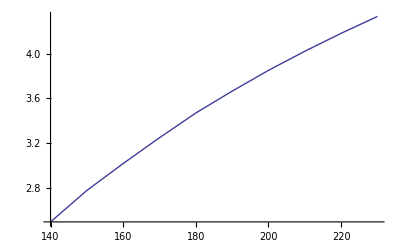

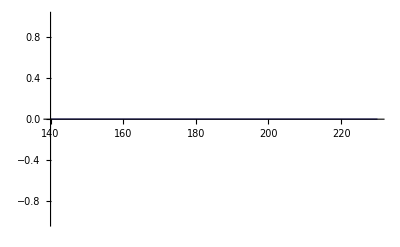

```mathematica
PrintRange[Extract[#,{{1},{2}}]&/@Union[ress,SameTest->(First[#1]==First[#2]&)]]
PrintRange[Extract[#,{{1},{4}}]&/@Union[ress,SameTest->(First[#1]==First[#2]&)]]
```

```mathematica
Take[#,2]&/@Union[ress,SameTest->(First[#1]==First[#2]&)]
```

```mathematica
FindRoot[Interpolation[Take[#,2]&/@ress,InterpolationOrder->1][Rm],{Rm,15}]
```

InterpolatingFunction::dmval: Input value {15.`} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {50.71428571428565`} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction will be suppressed during this calculation.

{Rm→50.7143}

```mathematica
3Mean[GetFields[#,{"δgamma","δomega"}]&/@$res]
```

{0.00348,0.00348}

```mathematica
Interpolation[Extract[#,{{1},{4}}]&/@ress,InterpolationOrder->1][15.577]//Expand
```

1.58626

#### Нахождение минимума порога по k

```mathematica
Rmvsk={{0.5,21,0.5,4.3,1.2},{0.6,15.37,0.03,0.7,0.2},{0.7,14.7,0.03,1.3,0.8},{0.8,15.6,0.01,2.1,0.05},{0.9,17.54,0.02,2.9,0.2},{1,20.57,0.02,4,0.5},{1.1,24.989,0.02,6.5,0.2},{1.2,31.58,0.03,9.91,0.03},{0.761803,15.13,0.03,1.68,0.05},{0.661803,14.71,0.03,1.09,0.03}};
```

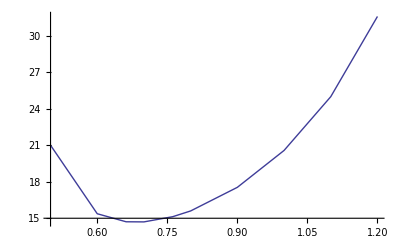

```mathematica
PrintRange[{#⟦1⟧,#⟦2⟧}&/@Union[Rmvsk]]
```

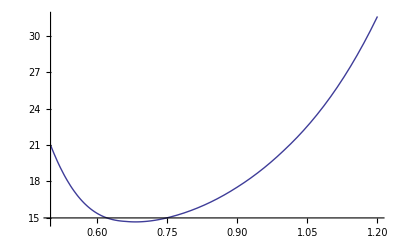

```mathematica
Plot[Interpolation[{#⟦1⟧,#⟦2⟧}&/@Rmvsk][t],{t,0.5,1.2}]
```

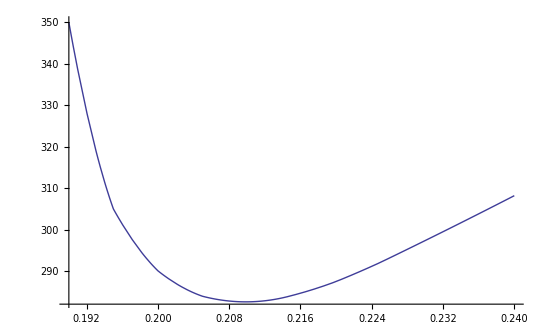

```mathematica
Plot[Interpolation[Select[{#[[1]],#[[2]]}&/@list,#[[1]]<2&],InterpolationOrder->2][t],{t,0.19,0.24}]
```

```mathematica
list=Sort[{2π#[[4]]/#[[1]],#[[2]],#[[3]]}&/@(GetFields[#,{"lfi","Rm","omega","m"}]&/@$res)]
```

{{0.7,141.808,8.70108},{0.704,141.774,8.89},{0.707,141.767,9.034},{0.71,141.775,9.1798},{0.713,141.797,9.327},{0.716,141.832,9.475},{0.719,141.879,9.626},{0.722,141.939,9.778},{0.725,142.01,9.931},{0.728,142.091,10.088},{0.731,142.184,10.2457},{0.734,142.287,10.404},{0.737,142.399,10.564},{0.74,142.522,10.727},{0.743,142.653,10.8909},{0.746,142.794,11.0569},{0.749,142.943,11.224},{0.75,142.995,11.2806},{0.752,143.101,11.3933},{0.755,143.266,11.564},{0.758,143.441,11.736},{0.761,143.622,11.911},{0.764,143.811,12.087},{0.767,144.009,12.2649},{0.77,144.295,12.4529},{0.8,146.603,14.339},{0.8,146.604,14.2396},{0.85,151.727,17.923},{0.9,157.848,22},{0.9,157.85,22.0589},{0.95,164.687,26.7745},{1,172.103,32.5},{1.,171.1,31.927},{1.05,180.008,38.5},{1.1,188.492,30},{1.2,206,60},{1.3,226.15,100}}

```mathematica
list={{0.7,141.808,8.70108},{0.704,141.7736,8.89},{0.707,141.7671,9.034},{0.7099999999999999,141.7752,9.1798},{0.7130000000000001,141.7971,9.327},{0.7160000000000001,141.8319,9.475},{0.719,141.8794,9.626},{0.722,141.9387,9.778},{0.725,142.0095,9.931},{0.728,142.0914,10.088},{0.7309999999999999,142.1839,10.2457},{0.7339999999999999,142.2866,10.404},{0.7369999999999999,142.3992,10.564},{0.74,142.5215,10.727}};
```

```mathematica
interp=Interpolation[{#[[1]],#[[2]]}&/@list,InterpolationOrder->2];
kcr=k/.FindRoot[interp'[k]==0,{k,0.7011}]
interp[kcr]
Interpolation[{#[[1]],#[[3]]}&/@list][kcr]
```

0.706836

141.767

9.02606

```mathematica
FindRoot[Interpolation[{#⟦1⟧,#⟦2⟧}&/@Rmvsk]'[t]==0,{t,0.7}]
```

{t→0.681981}

#### Нахождение минимума порога по chi

```mathematica
Rmvsχ={{1,14.69,0.03,1.21,0.03},{2,34.33,0.05,10.5,0.5},{0.5,49.788,0.05,11.3,0.2},{1.33,24,0.05,6.4,0.1},{0.8,17,0.05,2.19,0.2},{0.9,15.3,0.05,1.612,0.02}};
```

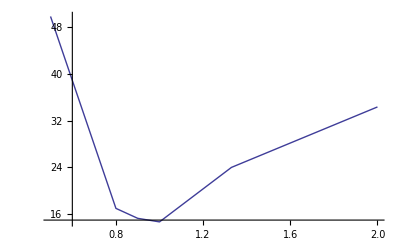

```mathematica
PrintRange[{#⟦1⟧,#⟦2⟧}&/@Union[Rmvsχ]]
```

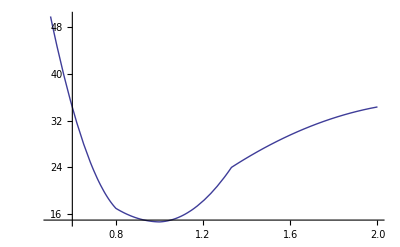

```mathematica
Plot[Interpolation[{#⟦1⟧,#⟦2⟧}&/@Rmvsχ,InterpolationOrder->2][t],{t,0.5,2}]
```

```mathematica
FindRoot[Interpolation[{#⟦1⟧,#⟦2⟧}&/@Rmvsχ,InterpolationOrder->2]'[t]==0,{t,0.7}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function.  You may need more than MachinePrecision digits of working precision to meet these tolerances.

{t→1.}

#### Нахождение минимума порога по chi и k методом Нелдера-Мида

NelderMead

```mathematica
f[x_,y_]:=Block[{tmp=Input["Type critical number Rm for κ="<>ToString[x]<>" and χ="<>ToString[y]]},
Print["f[κ=",x,";χ=",y,"]=",tmp];
Return[tmp];
]
```

```mathematica
NelderMead[vals_,f_,viv_:True]:=Block[{l,fh,fl,fr,fe,fg,fc,x0,xh,xr,xc,xe,α=1,β=0.5,γ=2,χ=0.5},
If[!SameQ@Dimensions[vals]∨(Most[#-First[vals]]&/@Rest[vals])<ArrayDepth[vals],Print["Points should form a simplex"];Return[$Failed]];
l=Sort[vals,Last[#1]>Last[#2]&];
fh=l⟦1,-1⟧;fg=l⟦2,-1⟧;fl=l⟦-1,-1⟧;
xh=Most[First[l]];
x0=Most[Mean[Rest[l]]];
xr=(1+α)x0-α xh;fr=f[Sequence@@xr];
If[fr<fl,
xe=(1+γ)x0-γ xh;If[viv,Print["extension point:",xe]];fe=f[Sequence@@xe];If[fe<fl,
Return[Prepend[Rest[l],Append[xe,fe]]],
Return[Prepend[Rest[l],Append[xr,fr]]]];
];
If[fr<fg,Return[Prepend[Rest[l],Append[xr,fr]]]];
If[fr<fh,fh=fr;xh=xr];
xc=(1-β)x0+β xh;If[viv,Print["shrinking point:",xc]];fc=f[Sequence@@xc];
If[fc<fh,Return[Prepend[Rest[l],Append[xc,fc]]]];
If[viv,Print["overall shrinking"]];
l=Append[(Last[l]+χ(Last[l]-#))&/@Prepend[Take[l,{2,-2}],Append[xh,fh]],Last[l]];
l=Append[Append[Most[#],f[Sequence@@Most[#]]]&/@Most[l],Last[l]];
Return[l];
]
```

```mathematica
init={{1,1,20.57},{0.9,1,17.54},{0.8,1,15.6},{0.7,1,14.7},{0.6,1,15.37},{1.1,1,24.989},{1.2,1,31.58},{0.761803,1,15.13},{0.668103,1,14.71},{0.685,1,14.69},{0.685*3,2,34.33},{0.685,0.5,49.788},{0.685*2,1.33,24},{0.685,0.8,17},{0.685,0.9,15.3},{0.585,0.9,14.978},{0.4275+2*0,0.85,20.55},{0.47,0.8,16.3},{0.7175,0.95,15.1203},{0.6175,0.95,14.8363},{0.58375,0.975,15.1678},{0.659375,0.9375,14.8235},{0.691875,0.9875,14.7273},{0.74513,1.03125,14.7991}};
```

```mathematica
Graphics3D[Line[{Join[Most[#],{14}],#}]&/@Select[init,Last[#]<20&],BoxRatios->1,Axes->True]
```

```mathematica
tmp=Select[KSubsets[init,3],MemberQ[Most/@init,NelderMead[#,Equal,False]]&];
```

```mathematica
Sort[init,Last[#1]>Last[#2]&]
```

{{0.685,0.5,49.788},{2.055,2,34.33},{1.2,1,31.58},{1.1,1,24.989},{1.37,1.33,24},{1,1,20.57},{0.855,0.85,20.55},{0.9,1,17.54},{0.685,0.8,17},{0.47,0.8,16.3},{0.8,1,15.6},{0.6,1,15.37},{0.685,0.9,15.3},{0.761803,1,15.13},{0.585,0.9,14.978},{0.668103,1,14.71},{0.7,1,14.7},{0.685,1,14.69}}

```mathematica
Manipulate[Graphics[Polygon[Most/@tri⟦n⟧],Axes->True,PlotRange->{{0.3,1.1},{0.85,1.05}},AspectRatio->1],{n,1,Length[tri],1}]
```

Сетка 20^3, r/R=0

```mathematica
tri={{{0.8,1,15.6},{0.685,0.9,15.3},{0.585,0.9,14.978}}};
```

```mathematica
AppendTo[tri,NelderMead[Last[tri],f,True]];
Last[tri]
```

f[κ=0.47;χ=0.8]=16.3

shrinking point:{0.7175,0.95}

f[κ=0.7175;χ=0.95]=15.1203

{{0.7175,0.95,15.1203},{0.685,0.9,15.3},{0.585,0.9,14.978}}

```mathematica
AppendTo[tri,NelderMead[Last[tri],f,True]];
Last[tri]
```

f[κ=0.6175;χ=0.95]=14.8363

extension point:{0.58375,0.975}

f[κ=0.58375;χ=0.975]=15.1678

{{0.6175,0.95,14.8363},{0.7175,0.95,15.1203},{0.585,0.9,14.978}}

```mathematica
AppendTo[tri,NelderMead[Last[tri],f,True]];
Last[tri]
```

f[κ=0.485;χ=0.9]=16

shrinking point:{0.659375,0.9375}

f[κ=0.659375;χ=0.9375]=14.8235

{{0.659375,0.9375,14.8235},{0.585,0.9,14.978},{0.6175,0.95,14.8363}}

```mathematica
AppendTo[tri,NelderMead[Last[tri],f,True]];
Last[tri]
```

f[κ=0.691875;χ=0.9875]=14.7273

extension point:{0.745313,1.03125}

f[κ=0.745313;χ=1.03125]=14.7991

{{0.745313,1.03125,14.7991},{0.6175,0.95,14.8363},{0.659375,0.9375,14.8235}}

```mathematica
AppendTo[tri,NelderMead[Last[tri],f,True]];
Last[tri]
```

f[κ=0.787188;χ=1.01875]=15.2379

shrinking point:{0.659922,0.967188}

f[κ=0.659922;χ=0.967188]=14.7264

{{0.659922,0.967188,14.7264},{0.659375,0.9375,14.8235},{0.745313,1.03125,14.7991}}

```mathematica
AppendTo[tri,NelderMead[Last[tri],f,True]];
Last[tri]
```

f[κ=0.745859;χ=1.06094]=14.714

extension point:{0.789102,1.12266}

f[κ=0.789102;χ=1.12266]=14.7889

{{0.745859,1.06094,14.714},{0.745313,1.03125,14.7991},{0.659922,0.967188,14.7264}}

```mathematica
AppendTo[tri,NelderMead[Last[tri],f,True]];
Last[tri]
```

f[κ=0.660469;χ=0.996875]=14.7129

extension point:{0.618047,0.979687}

f[κ=0.618047;χ=0.979687]=14.9274

{{0.660469,0.996875,14.7129},{0.659922,0.967188,14.7264},{0.745859,1.06094,14.714}}

```mathematica
NelderMead[Last[tri],f,True]
```

f[κ=0.746406;χ=1.09063]=$Canceled

shrinking point:{0.681543,0.998047}

f[κ=0.681543;χ=0.998047]=$Canceled

overall shrinking

f[κ=0.660742;χ=1.01172]=$Canceled

f[κ=0.617773;χ=0.964844]=$Canceled

{{0.660742,1.01172,$Canceled},{0.617773,0.964844,$Canceled},{0.660469,0.996875,14.7129}}

```mathematica
AppendTo[tri,%];
Last[tri]
```

{{0.660469,0.996875,14.7129},{0.659922,0.967188,14.7264},{0.745859,1.06094,14.714}}

### Зависимости

All data matches (True)&&(chi=1)&&(kalibr+BC="homogen"):

{4,5,6,7,8,9,11,12,13,14,15,16,22}

All such parameters={0,0.05,0.1,0.14,0.15,0.161422,0.181818,0.2,0.23,0.25,0.3,0.325,0.35,0.35555,0.375,0.4,0.425,0.45,0.45555,0.475,0.5,0.52,0.525,0.54,0.55,0.55555,0.56,0.575,0.58,0.6,0.62,0.625,0.64,0.65,0.66,0.675,0.68,0.7,0.7091,0.725,0.75,0.759091,0.775,0.8,0.809091,0.825,0.85,0.859091,0.875,0.9,0.909091,0.925,0.95,0.975,1,1.}

{Nxz,Ny,TDV,Re,ksi,chi,lfi,wall,Rvac,etawall,Rm,m,kalibr+BC}

Plots can be shown for parameters:

№1:{Nxz→64,Ny→64,TDV→0,Re→80,ksi→∞,chi→1,lfi→2 π,wall→0,Rvac→2,etawall→0,Rm→250,m→1,kalibr+BC→homogen}, number of points=2

№2:{Nxz→64,Ny→30,TDV→0,Re→0,ksi→∞,chi→1,lfi→6.28319,wall→0,Rvac→3,etawall→0,Rm→19,m→1,kalibr+BC→homogen}, number of points=2

№3:{Nxz→64,Ny→30,TDV→0,Re→0,ksi→∞,chi→1,lfi→6.28319,wall→0,Rvac→3,etawall→0,Rm→20,m→1,kalibr+BC→homogen}, number of points=2

№4:{Nxz→64,Ny→30,TDV→0,Re→0,ksi→∞,chi→1,lfi→6.28319,wall→0,Rvac→3,etawall→0,Rm→21,m→1,kalibr+BC→homogen}, number of points=2

№5:{Nxz→64,Ny→30,TDV→0,Re→0,ksi→∞,chi→1,lfi→6.28319,wall→0,Rvac→3,etawall→0,Rm→22,m→1,kalibr+BC→homogen}, number of points=2

№6:{Nxz→64,Ny→30,TDV→0,Re→0,ksi→∞,chi→1,lfi→6.28319,wall→0,Rvac→3,etawall→0,Rm→23,m→1,kalibr+BC→homogen}, number of points=2

№7:{Nxz→64,Ny→30,TDV→0,Re→0,ksi→∞,chi→1,lfi→6.98132,wall→0,Rvac→3,etawall→0,Rm→16,m→1,kalibr+BC→homogen}, number of points=3

№8:{Nxz→64,Ny→30,TDV→0,Re→0,ksi→∞,chi→1,lfi→6.98132,wall→0,Rvac→3,etawall→0,Rm→17,m→1,kalibr+BC→homogen}, number of points=3

№9:{Nxz→64,Ny→30,TDV→0,Re→0,ksi→∞,chi→1,lfi→6.98132,wall→0,Rvac→3,etawall→0,Rm→18,m→1,kalibr+BC→homogen}, number of points=3

№10:{Nxz→64,Ny→30,TDV→0,Re→0,ksi→∞,chi→1,lfi→6.98132,wall→0,Rvac→3,etawall→0,Rm→19,m→1,kalibr+BC→homogen}, number of points=3

№11:{Nxz→64,Ny→30,TDV→0,Re→0,ksi→∞,chi→1,lfi→15.708,wall→0,Rvac→3,etawall→0,Rm→14,m→1,kalibr+BC→homogen}, number of points=2

№12:{Nxz→64,Ny→30,TDV→0,Re→0,ksi→∞,chi→1,lfi→15.708,wall→0,Rvac→3,etawall→0,Rm→15,m→1,kalibr+BC→homogen}, number of points=2

№13:{Nxz→64,Ny→30,TDV→0,Re→0,ksi→∞,chi→1,lfi→15.708,wall→0,Rvac→3,etawall→0,Rm→16,m→1,kalibr+BC→homogen}, number of points=2

№14:{Nxz→64,Ny→30,TDV→0,Re→0,ksi→∞,chi→1,lfi→15.708,wall→0,Rvac→3,etawall→0,Rm→17,m→1,kalibr+BC→homogen}, number of points=2

№15:{Nxz→64,Ny→30,TDV→0,Re→0,ksi→∞,chi→1,lfi→8.97598,wall→0,Rvac→3,etawall→0,Rm→13,m→1,kalibr+BC→homogen}, number of points=4

№16:{Nxz→64,Ny→30,TDV→0,Re→0,ksi→∞,chi→1,lfi→8.97598,wall→0,Rvac→3,etawall→0,Rm→14,m→1,kalibr+BC→homogen}, number of points=4

№17:{Nxz→64,Ny→30,TDV→0,Re→0,ksi→∞,chi→1,lfi→8.97598,wall→0,Rvac→3,etawall→0,Rm→15,m→1,kalibr+BC→homogen}, number of points=4

№18:{Nxz→64,Ny→30,TDV→0,Re→0,ksi→∞,chi→1,lfi→8.97598,wall→0,Rvac→3,etawall→0,Rm→16,m→1,kalibr+BC→homogen}, number of points=4

№19:{Nxz→64,Ny→30,TDV→0,Re→0,ksi→∞,chi→1,lfi→12.5664,wall→0,Rvac→3,etawall→0,Rm→14,m→1,kalibr+BC→homogen}, number of points=2

№20:{Nxz→64,Ny→30,TDV→0,Re→0,ksi→∞,chi→1,lfi→10.472,wall→0,Rvac→3,etawall→0,Rm→11,m→1,kalibr+BC→homogen}, number of points=2

№21:{Nxz→64,Ny→30,TDV→0,Re→0,ksi→∞,chi→1,lfi→10.472,wall→0,Rvac→3,etawall→0,Rm→13.5,m→1,kalibr+BC→homogen}, number of points=2

№22:{Nxz→64,Ny→30,TDV→0,Re→0,ksi→∞,chi→1,lfi→10.472,wall→0,Rvac→3,etawall→0,Rm→16,m→1,kalibr+BC→homogen}, number of points=5

№23:{Nxz→20,Ny→20,TDV→0,Re→0,ksi→∞,chi→1,lfi→14,wall→0,Rvac→2,etawall→1,Rm→30,m→1,kalibr+BC→homogen}, number of points=2

№24:{Nxz→20,Ny→20,TDV→0,Re→0,ksi→∞,chi→1,lfi→6.28319,wall→0,Rvac→2,etawall→1,Rm→50,m→1,kalibr+BC→homogen}, number of points=2

№25:{Nxz→20,Ny→20,TDV→0,Re→0,ksi→∞,chi→1,lfi→6.28319,wall→0,Rvac→2,etawall→1,Rm→40,m→1,kalibr+BC→homogen}, number of points=2

№26:{Nxz→20,Ny→20,TDV→0,Re→0,ksi→∞,chi→1,lfi→6.28319,wall→0,Rvac→2,etawall→1,Rm→30,m→1,kalibr+BC→homogen}, number of points=2

№27:{Nxz→20,Ny→20,TDV→0,Re→0,ksi→∞,chi→1,lfi→6.28319,wall→0,Rvac→2,etawall→1,Rm→20,m→1,kalibr+BC→homogen}, number of points=2

№28:{Nxz→20,Ny→20,TDV→0,Re→0,ksi→∞,chi→1,lfi→6.28319,wall→0,Rvac→2,etawall→1,Rm→10,m→1,kalibr+BC→homogen}, number of points=2

№29:{Nxz→64,Ny→30,TDV→0,Re→0,ksi→∞,chi→1,lfi→12.5664,wall→0,Rvac→3,etawall→0,Rm→19,m→1,kalibr+BC→homogen}, number of points=2

№30:{Nxz→64,Ny→30,TDV→0,Re→0,ksi→∞,chi→1,lfi→10.472,wall→0,Rvac→3,etawall→0,Rm→12,m→1,kalibr+BC→homogen}, number of points=3

№31:{Nxz→64,Ny→30,TDV→0,Re→0,ksi→∞,chi→1,lfi→10.472,wall→0,Rvac→3,etawall→0,Rm→13,m→1,kalibr+BC→homogen}, number of points=4

№32:{Nxz→64,Ny→30,TDV→0,Re→0,ksi→∞,chi→1,lfi→10.472,wall→0,Rvac→3,etawall→0,Rm→14,m→1,kalibr+BC→homogen}, number of points=4

№33:{Nxz→64,Ny→30,TDV→0,Re→0,ksi→∞,chi→1,lfi→10.472,wall→0,Rvac→3,etawall→0,Rm→15,m→1,kalibr+BC→homogen}, number of points=4

№34:{Nxz→64,Ny→30,TDV→0,Re→0,ksi→∞,chi→1,lfi→7.854,wall→0,Rvac→3,etawall→0,Rm→16,m→1,kalibr+BC→homogen}, number of points=2

№35:{Nxz→64,Ny→30,TDV→0,Re→0,ksi→∞,chi→1,lfi→7.854,wall→0,Rvac→3,etawall→0,Rm→17,m→1,kalibr+BC→homogen}, number of points=2

№36:{Nxz→64,Ny→30,TDV→0,Re→0,ksi→∞,chi→1,lfi→7.854,wall→0,Rvac→3,etawall→0,Rm→18,m→1,kalibr+BC→homogen}, number of points=2

№37:{Nxz→64,Ny→30,TDV→0,Re→0,ksi→∞,chi→1,lfi→12.5664,wall→0,Rvac→3,etawall→0,Rm→21.5,m→1,kalibr+BC→homogen}, number of points=2

№38:{Nxz→64,Ny→32,TDV→0,Re→0,ksi→∞,chi→1,lfi→8.97598,wall→0,Rvac→3,etawall→0,Rm→14,m→1,kalibr+BC→homogen}, number of points=2

№39:{Nxz→64,Ny→32,TDV→0,Re→0,ksi→∞,chi→1,lfi→8.97598,wall→0,Rvac→3,etawall→0,Rm→15,m→1,kalibr+BC→homogen}, number of points=2

№40:{Nxz→64,Ny→32,TDV→0,Re→0,ksi→∞,chi→1,lfi→8.97598,wall→0,Rvac→3,etawall→0,Rm→16,m→1,kalibr+BC→homogen}, number of points=2

So constant parameters are:

{Nxz→64,Ny→30,TDV→0,Re→0,ksi→∞,chi→1,lfi→10.472,wall→0,Rvac→3,etawall→0,Rm→16,m→1,kalibr+BC→homogen}

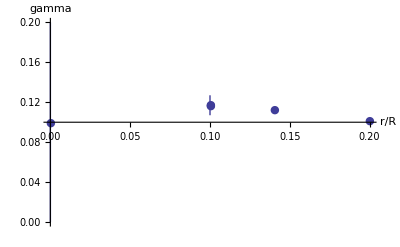
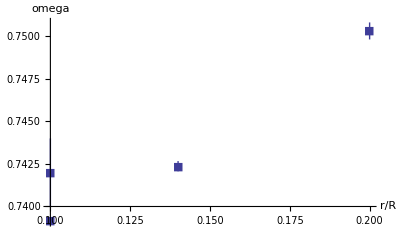

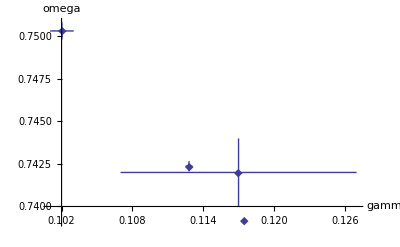

```mathematica
ShowDependance["r/R",{"kalibr+BC"->"homogen","chi"->1}]
```

```mathematica
ShowDependance["omega"]
```

All data matches (True):

Wrong parameter

```mathematica
$res=GetResults[{"Nxz"->64,"Ny"->30,"TDV"->0,"ADV"->0,"ksi"->∞,"chi"->1,"lfi"->10.472,"wall"->0,"Rvac"->3,"etawall"->0,"Rm"->16,"m"->1,"kalibr+BC"->"homogen"}]
```

All data matches (True)&&(ADV=0)&&(chi=1)&&(etawall=0)&&(kalibr+BC="homogen")&&(ksi=Infinity)&&(lfi=10.472)&&(m=1)&&(Nxz=64)&&(Ny=30)&&(Rm=16)&&(Rvac=3)&&(TDV=0)&&(wall=0):

{{2008,4,1,64,30,0,0,∞,1,0,10.472,0,3,0,16,1,1,0.1,0.1,?,?,homogen},{2008,4,10,64,30,0,0,∞,1,0.1,10.472,0,3,0,16,1,1,0.117,0.01,0.742,0.002,homogen},{2008,4,10,64,30,0,0,∞,1,0.1,10.472,0,3,0,16,1,1,0.11752,0.0001,0.739188,0.0001,homogen},{2008,4,11,64,30,0,0,∞,1,0.2,10.472,0,3,0,16,1,1,0.102031,0.001,0.750317,0.0005,homogen},{2008,4,24,64,30,0,0,∞,1,0.14,10.472,0,3,0,16,1,1,0.1128,0.0003,0.742368,0.0003,homogen}}

```mathematica
PrintRange[Union[GetFields[#,{"r/R","omega"}]&/@$res]]
```

```mathematica
pts//TableForm
```

0 | 0.1 | 0.1 | ? | ? | homogen
0.1 | 0.11752 | 0.0001 | 0.739188 | 0.0001 | homogen
0.1 | 0.117 | 0.01 | 0.742 | 0.002 | homogen
0.14 | 0.1128 | 0.0003 | 0.742368 | 0.0003 | homogen
0.2 | 0.102031 | 0.001 | 0.750317 | 0.0005 | homogen

All data matches (True)&&(r/R=0):

{4,5,6,7,8,9,10,12,13,14,15,16,22}

All such parameters={5.23599,5.71199,6.28319,6.28319,6.98132,6.98132,7.85398,7.85398,7.96245,7.98181,8.18013,8.42409,8.43026,8.75705,8.97598,8.97598,9.08139,9.17253,9.49404,9.51322,9.5211,9.529,10.1662,10.1752,10.472,10.7405,10.7635,12.5664,12.5664,12.955,13.3685,14,14.6975,15.708,16.213,20.944,91.7253,2 π}

{Nxz,Ny,TDV,ADV,ksi,chi,r/R,wall,Rvac,etawall,Rm,m,kalibr+BC}

Plots can be shown for parameters:

№1:{Nxz→20,Ny→20,TDV→0,ADV→0,ksi→∞,chi→1,r/R→0,wall→0,Rvac→2,etawall→1,Rm→12.5,m→1,kalibr+BC→homogen}, number of points=7

№2:{Nxz→20,Ny→20,TDV→0,ADV→0,ksi→∞,chi→1,r/R→0,wall→0,Rvac→2,etawall→1,Rm→15,m→1,kalibr+BC→homogen}, number of points=11

№3:{Nxz→20,Ny→20,TDV→0,ADV→0,ksi→∞,chi→1,r/R→0,wall→0,Rvac→2,etawall→1,Rm→17.5,m→1,kalibr+BC→homogen}, number of points=7

№4:{Nxz→20,Ny→20,TDV→0,ADV→0,ksi→∞,chi→1,r/R→0,wall→0,Rvac→2,etawall→1,Rm→20,m→1,kalibr+BC→homogen}, number of points=11

№5:{Nxz→20,Ny→20,TDV→0,ADV→0,ksi→∞,chi→1,r/R→0,wall→0,Rvac→2,etawall→1,Rm→22.5,m→1,kalibr+BC→homogen}, number of points=7

№6:{Nxz→20,Ny→20,TDV→0,ADV→0,ksi→∞,chi→1,r/R→0,wall→0,Rvac→2,etawall→1,Rm→25,m→1,kalibr+BC→homogen}, number of points=8

№7:{Nxz→20,Ny→20,TDV→0,ADV→0,ksi→∞,chi→1,r/R→0,wall→0,Rvac→2,etawall→1,Rm→27.5,m→1,kalibr+BC→homogen}, number of points=7

№8:{Nxz→20,Ny→20,TDV→0,ADV→0,ksi→∞,chi→1,r/R→0,wall→0,Rvac→2,etawall→1,Rm→30,m→1,kalibr+BC→homogen}, number of points=11

№9:{Nxz→20,Ny→20,TDV→0,ADV→0,ksi→∞,chi→1,r/R→0,wall→0,Rvac→2,etawall→1,Rm→50,m→1,kalibr+BC→homogen}, number of points=2

№10:{Nxz→20,Ny→20,TDV→0,ADV→0,ksi→∞,chi→1,r/R→0,wall→0,Rvac→2,etawall→1,Rm→40,m→1,kalibr+BC→homogen}, number of points=2

№11:{Nxz→20,Ny→20,TDV→0,ADV→0,ksi→∞,chi→1,r/R→0,wall→0,Rvac→2,etawall→1,Rm→10,m→1,kalibr+BC→homogen}, number of points=3

№12:{Nxz→64,Ny→30,TDV→0,ADV→0,ksi→∞,chi→1,r/R→0,wall→0,Rvac→3,etawall→0,Rm→19,m→1,kalibr+BC→homogen}, number of points=2

№13:{Nxz→64,Ny→30,TDV→0,ADV→0,ksi→∞,chi→1,r/R→0,wall→0,Rvac→3,etawall→0,Rm→16,m→1,kalibr+BC→homogen}, number of points=7

№14:{Nxz→64,Ny→30,TDV→0,ADV→0,ksi→∞,chi→1,r/R→0,wall→0,Rvac→3,etawall→0,Rm→17,m→1,kalibr+BC→homogen}, number of points=3

№15:{Nxz→64,Ny→30,TDV→0,ADV→0,ksi→∞,chi→1,r/R→0,wall→0,Rvac→3,etawall→0,Rm→14,m→1,kalibr+BC→homogen}, number of points=5

№16:{Nxz→64,Ny→30,TDV→0,ADV→0,ksi→∞,chi→1,r/R→0,wall→0,Rvac→3,etawall→0,Rm→15,m→1,kalibr+BC→homogen}, number of points=5

№17:{Nxz→20,Ny→20,TDV→0,ADV→0,ksi→∞,chi→0.95,r/R→0,wall→0,Rvac→2,etawall→1,Rm→15.2,m→1,kalibr+BC→homogen}, number of points=2

№18:{Nxz→20,Ny→20,TDV→0,ADV→0,ksi→∞,chi→0.95,r/R→0,wall→0,Rvac→2,etawall→1,Rm→15,m→1,kalibr+BC→homogen}, number of points=3

№19:{Nxz→64,Ny→30,TDV→0,ADV→0,ksi→∞,chi→1,r/R→0,wall→0,Rvac→3,etawall→0,Rm→13,m→1,kalibr+BC→homogen}, number of points=3

№20:{Nxz→20,Ny→20,TDV→0,ADV→0,ksi→∞,chi→0.9,r/R→0,wall→0,Rvac→2,etawall→1,Rm→15,m→1,kalibr+BC→homogen}, number of points=3

№21:{Nxz→30,Ny→30,TDV→0,ADV→0,ksi→∞,chi→1,r/R→0,wall→0,Rvac→3,etawall→1,Rm→17.5,m→1,kalibr+BC→homogen}, number of points=4

№22:{Nxz→30,Ny→30,TDV→0,ADV→0,ksi→∞,chi→1,r/R→0,wall→0,Rvac→3,etawall→1,Rm→10,m→1,kalibr+BC→homogen}, number of points=2

№23:{Nxz→30,Ny→30,TDV→0,ADV→0,ksi→∞,chi→1,r/R→0,wall→0,Rvac→3,etawall→1,Rm→12.5,m→1,kalibr+BC→homogen}, number of points=3

№24:{Nxz→30,Ny→30,TDV→0,ADV→0,ksi→∞,chi→1,r/R→0,wall→0,Rvac→3,etawall→1,Rm→15,m→1,kalibr+BC→homogen}, number of points=3

№25:{Nxz→30,Ny→30,TDV→0,ADV→0,ksi→∞,chi→1,r/R→0,wall→0,Rvac→3,etawall→1,Rm→20,m→1,kalibr+BC→homogen}, number of points=2

So constant parameters are:

{Nxz→20,Ny→20,TDV→0,ADV→0,ksi→∞,chi→1,r/R→0,wall→0,Rvac→2,etawall→1,Rm→20,m→1,kalibr+BC→homogen}

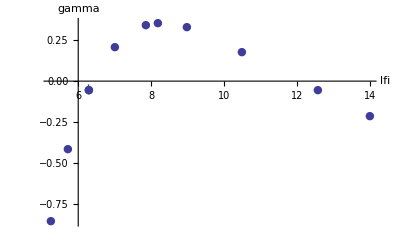
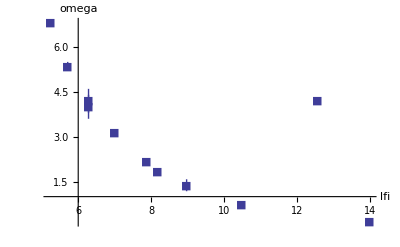

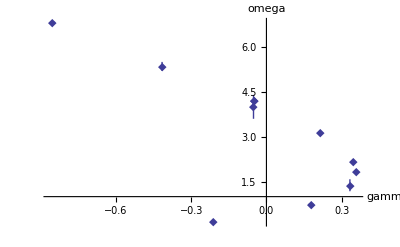

```mathematica
ShowDependance["lfi",{And[True,"r/R"->0]}]
```

#### От тороидальности

```mathematica
$res=GetResults[{"chi"->1,"Rm">5,"kalibr+BC"->"homogen"}];
```

All data matches (Rm>5)&&(chi=1)&&(kalibr+BC="homogen"):

```mathematica
Length/@(GetResults[{"chi"->1,"Rm">5,"kalibr+BC"->"homogen","lfi"->#}]&/@lfis)
```

{1,9,8,17,10,8,18,6,4,8,15,3,5,6,8,26,5,2,3,6,64,7,5,4,7,5,17,5,3,14,4,5,1}

```mathematica
lfis=Union@(GetField[#,"lfi"]&/@GetResults[{"chi"->1,"kalibr+BC"->"homogen","Nxz">30}])
```

All data matches (Nxz>30)&&(chi=1)&&(kalibr+BC="homogen"):

{3.5,6.28319,6.28319,6.98132,7.78479,7.85398,7.854,8.37758,8.63939,8.97598,9.10607,9.73099,10.472,11.22,11.5192,12.5664,12.5664,12.5664,12.9747,15.708,20.944}

```mathematica
Transpose[{Range[Length[lfis]],lfis}]
```

{{1,3.5},{2,5.23599},{3,5.71199},{4,6.28319},{5,6.28319},{6,6.98132},{7,6.98132},{8,7.78479},{9,7.85398},{10,7.85398},{11,7.854},{12,8.18013},{13,8.37758},{14,8.63939},{15,8.97598},{16,8.97598},{17,9.10607},{18,9.17253},{19,9.49404},{20,9.73099},{21,10.472},{22,11.22},{23,11.5192},{24,12.5664},{25,12.5664},{26,12.5664},{27,12.5664},{28,12.9747},{29,14},{30,15.708},{31,16.213},{32,20.944},{33,91.7253}}

```mathematica
Union[GetField[#,"r/R"]&/@GetResults[{"chi"->1,"Rm">5,"kalibr+BC"->"homogen","lfi"->lfis⟦27⟧}]]
```

All data matches (Rm>5)&&(chi=1)&&(kalibr+BC="homogen")&&(lfi=12.5664):

{0,0.1,0.25}

```mathematica
$res1=Union[GetResults[{"chi"->1,"Rm">5,"kalibr+BC"->"homogen","Nxz">30,"lfi"->lfis⟦6⟧}],GetResults[{"chi"->1,"Rm">5,"kalibr+BC"->"homogen","Nxz">30,"lfi"->lfis⟦7⟧}]];
```

```mathematica
$res1=Union[GetResults[{"chi"->1,"Rm">5,"kalibr+BC"->"homogen","Nxz">30,"lfi"->lfis⟦9⟧}],GetResults[{"chi"->1,"Rm">5,"kalibr+BC"->"homogen","Nxz">30,"lfi"->lfis⟦10⟧}],GetResults[{"chi"->1,"Rm">5,"kalibr+BC"->"homogen","Nxz">30,"lfi"->lfis⟦11⟧}]];
```

```mathematica
$res1=Union[GetResults[{"chi"->1,"Rm">5,"kalibr+BC"->"homogen","Nxz">30,"lfi"->lfis⟦15⟧}],GetResults[{"chi"->1,"Rm">5,"kalibr+BC"->"homogen","Nxz">30,"lfi"->lfis⟦16⟧}]];
```

```mathematica
$res1=GetResults[{"chi"->1,"Rm">5,"kalibr+BC"->"homogen","Rvac"≥3,"Nxz">30,"lfi"->lfis⟦21⟧}];
```

```mathematica
$res1=Union[GetResults[{"chi"->1,"Rm">5,"kalibr+BC"->"homogen","Nxz">30,"lfi"->lfis⟦25⟧}],GetResults[{"chi"->1,"Rm">5,"kalibr+BC"->"homogen","Nxz">30,"lfi"->lfis⟦26⟧}],GetResults[{"chi"->1,"Rm">5,"kalibr+BC"->"homogen","Nxz">30,"lfi"->lfis⟦27⟧}]];
```

```mathematica
Select[MapThread[Join[{#1},#2]&,{fields,Union/@Transpose[$res1]}],Length[#]>2∧!MemberQ[{"month","day"},First[#]]&]//TableForm
```

r/R | 0 | 0.1 | 0.25 |  |  |  |  |  |  |  |  |  |  |  |  | 
lfi | 12.5664 | 12.5664 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Rm | 12 | 13 | 14 | 15 | 16 | 16.5 | 19 | 21.5 | 23 | 24 |  |  |  |  |  | 
n | 1 | 2 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
gamma | -0.07 | -0.04 | -0.036 | -0.034 | -0.006 | -0.005 | 0.02 | 0.04 | 0.044 | 0.05 | 0.09 | 0.094 | 0.1 | 0.1829 | 0.2087 | 
δgamma | 0.0001 | 0.001 | 0.003 | 0.005 | 0.01 | 0.03 | 0.05 |  |  |  |  |  |  |  |  | 
omega | 0.24 | 0.25 | 0.3 | 0.32 | 0.332 | 0.336 | 0.35 | 0.36 | 0.37 | 0.38 | 0.384 | 0.39 | 0.4 | 4.45 | 4.655 | 4.83
δomega | 0.01 | 0.02 | 0.05 | 0.1 | 0.15 |  |  |  |  |  |  |  |  |  |  |

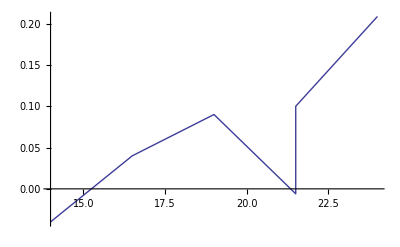

```mathematica
PrintRange[Take[#,{2,3}]&/@Union@Select[GetFields[#,{"r/R","Rm","gamma","omega"}]&/@$res1,First[#]==0.25&]]
```

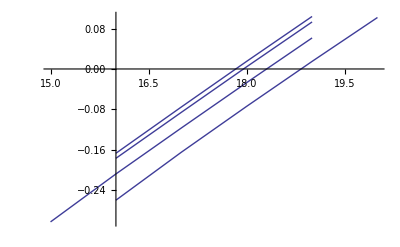

```mathematica
Show[%102,%101,%100,%107](*k=0.9*)
```

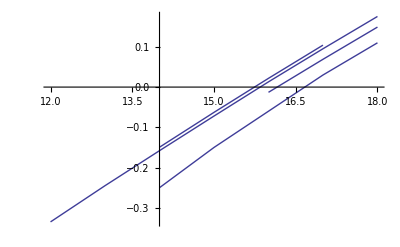

```mathematica
Show[%117,%119,%120,%121](*k=0.8*)
```

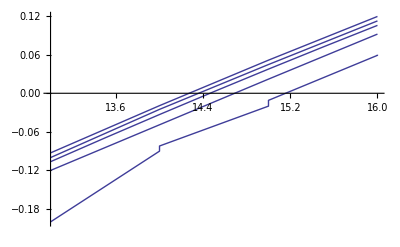

```mathematica
Show[%137,%132,%133,%134,%135](*k=0.7*)
```

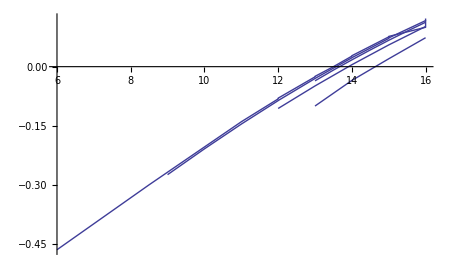

```mathematica
Show[%172,%148,%149,%150,%164](*k=0.6*)
```

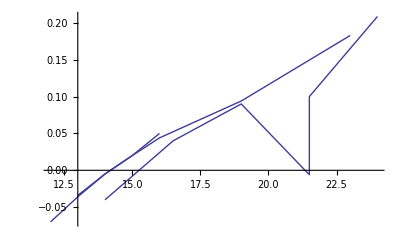

```mathematica
Show[%226,%228,%229](*k=0.5*)
```

### Универсальные функции

```mathematica
Rmcrk[κ_,n_,Rmin_:2]:=Block[{data={#[[3]],#[[2]],#[[4]]}&/@Select[GetFields[#,{"r/R","Rm","gamma","δgamma","Rvac","lfi","n"}]&/@$res,First[#]==κ∧Abs[(2π)/(First[#]#⟦-2⟧)Last[#]-n]<0.01∧#⟦-3⟧≥Rmin∧#⟦4⟧≤0.2&],d},
If[Length[d=Select[data,Abs[#⟦1⟧]<0.8#⟦3⟧<0.17&]]==1,Return[d⟦1,2⟧]];
If[Length[Select[data,Abs[#⟦1⟧]>#⟦3⟧&]]==0,Return[{0,0}]];
If[Length[data]<2,{0,0},
Fit[Most/@data,{1,x,x^2},x]/.x->0
]
];
```

```mathematica
ns[n_]:=If[Length[l=Reverse@Select[{1/#,Rmcrk[#,n,1]}&/@κs,Last[#]>0&]]>0,l,{{0,0}}]
```

```mathematica
TransX[l_List,pow_:1]:={#⟦1⟧,(√(1+(#⟦1⟧)^2))^pow#⟦2⟧}&/@l;
TransX1[l_List,mul_:√2.]:={#⟦1⟧,mul #⟦2⟧}&/@l;
```

```mathematica
κs=Union[GetField[#,"r/R"]&/@$res]
```

{0.1,0.14,0.15,0.161422,0.181818,0.2,0.23,0.25,0.3,0.325,0.35,0.35555,0.375,0.4,0.425,0.45,0.45555,0.475,0.5,0.52,0.525,0.54,0.55,0.55555,0.56,0.575,0.58,0.6,0.62,0.625,0.64,0.65,0.66,0.675,0.68,0.7,0.7091,0.725,0.75,0.759091,0.775,0.8,0.809091,0.825,0.85,0.859091,0.875,0.9,0.909091,0.925,0.95,0.975,1,1.}

```mathematica
ns[2]
```

{{1.90476,22.7791},{2.,21.1305},{2.10526,19.8141},{2.22222,18.7056},{2.85714,17.254}}

```mathematica
ns[1]
```

{{1.81818,37.8557}}

### Astronomische Nacrhicten

```mathematica
$res=GetResults[{"r/R">0.05,"chi"->1,"wall"->0,"Nxz">60,"Rm"<1000}];Length[$res]
```

All data matches (r/R>0.05&&Nxz>60&&Rm<1000)&&(chi=1)&&(wall=0):

339

```mathematica
vsr[κ_,χ_]:=1/π NIntegrate[Sqrt[(1+κ ρ Cos[ϕ])^2+ρ^2 χ^2]ρ,{ρ,0,1},{ϕ,0,2π}]
```

```mathematica
vmax[κ_,χ_]:=√(1+χ^2/(1-κ)^2)
```

```mathematica
κs=Union[GetField[#,"r/R"]&/@$res]
```

{0.8}

```mathematica
Rmcrk[0.55,2,1]
```

6.66667

```mathematica
Select[$res,GetField[#,"r/R"]==0.5&]
```

{{2010,7,13,64,32,0,0,∞,1,0.5,4 π,0,2,0,100,1,2,5.216,0.02,13.179,0.001,homogen},{2010,7,16,64,32,0,0,∞,1,0.5,12.5664,0,2,1,23.5,1,2,0,0.1,0.6,0.5,homogen},{2010,8,20,128,64,0,0,∞,1,0.5,12.5664,0,3,1,48,1,2,2.02,0.01,0,10,homogen},{2010,8,20,128,64,0,0,∞,1,0.5,12.5664,0,3,1,50,1,2,2.165,0.01,0,10,homogen},{2010,8,20,128,64,0,0,∞,1,0.5,12.5664,0,3,1,52,1,2,2.31,0.01,0,10,homogen},{2010,8,20,128,64,0,0,∞,1,0.5,12.5664,0,3,1,54,1,2,2.45,0.01,0,10,homogen},{2010,8,20,128,64,0,0,∞,1,0.5,12.5664,0,3,1,56,1,2,2.59,0.01,0,10,homogen},{2010,8,20,128,64,0,0,∞,1,0.5,12.5664,0,3,1,58,1,2,2.715,0.01,0,10,homogen},{2010,8,24,128,64,0,0,∞,1,0.5,12.5664,0,3,1,20,1,1,-0.045,0.005,0,10,homogen},{2010,8,24,128,64,0,0,∞,1,0.5,12.5664,0,3,1,22,1,1,-0.022,0.005,0,10,homogen},{2010,8,24,128,64,0,0,∞,1,0.5,12.5664,0,3,1,24,1,1,-0.0025,0.0025,0,10,homogen},{2010,8,24,128,64,0,0,∞,1,0.5,12.5664,0,3,1,26,1,1,0.015,0.005,0,10,homogen}}

```mathematica
(2π GetField[#,"n"])/(GetField[#,"r/R"]GetField[#,"lfi"])&/@%
```

{2.}

```mathematica
PrintRange[Sort[Take[#,{15,18,3}]&/@Select[$res,GetField[#,"r/R"]==0.6&]]]
```

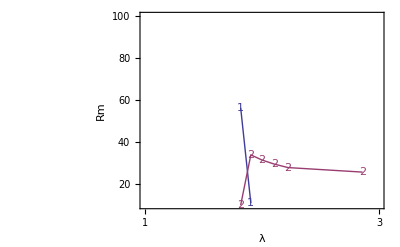

```mathematica
Show[ListPlot[TransX1[#,√(1+1.1^2)]&/@{ns[1],ns[2],ns[3]},PlotMarkers->{1,2,x,o,-Graphics-,-Graphics-,5,6},Joined->True],Graphics[{Dashed,Line[{{3.83,20},{3.83,35}}]}],PlotRange->{{1,3},{10,100}},FrameLabel->{"λ","Rm"},FrameTicks->{{Automatic,None},{Range[10],None}},Frame->True,BaseStyle->{FontFamily->"Times",FontSize->20},AxesOrigin->{0,0}]
```

```mathematica
GetResults[{"r/R">0.60,"r/R"<0.68,"chi"->1,"Rvac">1,"wall"->0,"Nxz">30,"n"->1}]
```

All data matches (r/R>0.6&&r/R<0.68&&Rvac>1&&Nxz>30)&&(chi=1)&&(n=1)&&(wall=0):

```mathematica
ListPlot[{(#[[2]])/(2π),√2#[[3]]}&/@(GetFields[#,{"r/R","lfi","Rm","omega","n"}]&/@%),PlotStyle->PointSize[0.04]]
```

```mathematica
TransX1[l_List,mul_:√2]:={#⟦1⟧,mul #⟦2⟧}&/@l;
```

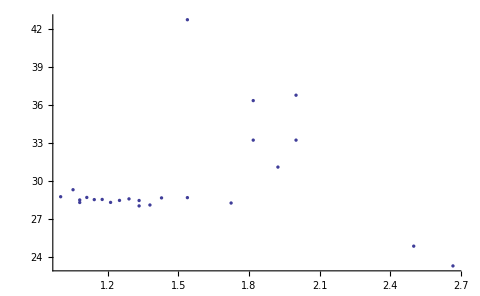

```mathematica
g=ListPlot[{1/#[[1]],√2#[[3]]}&/@Select[GetFields[#,{"r/R","lfi","Rm","omega","n","chi","gamma","δgamma"}]&/@$res,Abs[#⟦-2⟧]<0.8#⟦-1⟧∧#⟦-1⟧<0.15&],PlotStyle->PointSize[0.005],PlotRange->{10,All},AxesOrigin->{1,10}]
```

```mathematica
g1=ListPlot[{1/#,√2 Rmcrk[#,1]}&/@κs,PlotMarkers->1];
g2=ListPlot[{1/#,√2 Rmcrk[#,2]}&/@κs,PlotMarkers->2];
```

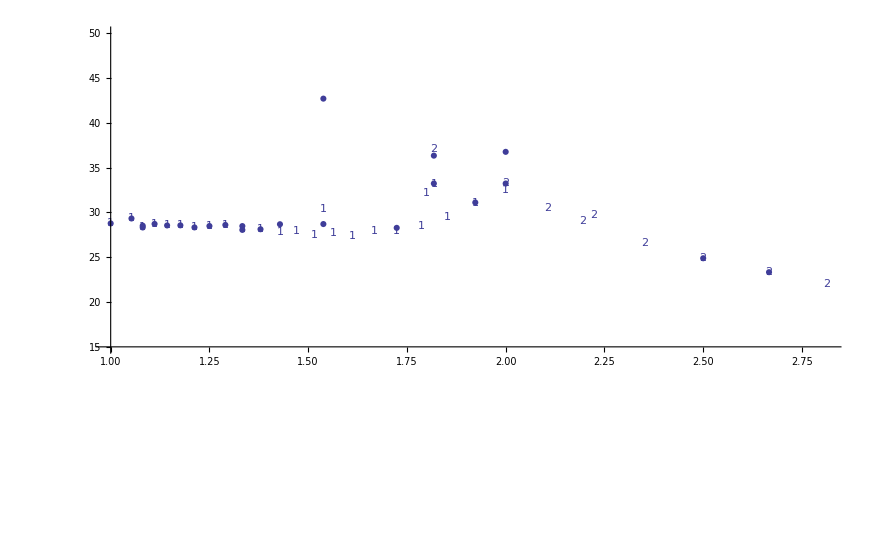

```mathematica
Show[g,g1,g2,PlotRange->{15,50},AxesOrigin->{1,15},Epilog->Point[{}]]
```

```mathematica
ListPlot[{1/First[#],Last[#]}&/@(GetFields[#,{"r/R","omega","gamma"}]&/@Select[GetResults[{"r/R">0.3,"chi"->0.9,"wall"->0,"Nxz">60,"Nxz"<2500,"Rm"<1000}],Abs[(2π)/(GetField[#,"r/R"]GetField[#,"lfi"])GetField[#,"n"]-1]<0.01&]),AxesOrigin->{1,0},PlotRange->All]
```

All data matches (r/R>0.1&&Nxz>60&&Nxz<2500&&Rm<1000)&&(chi=1)&&(wall=0):

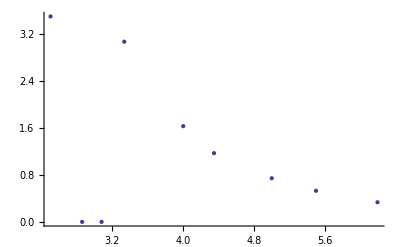

```mathematica
ListPlot[{1/First[#],Last[#]}&/@(Most[First[SortBy[#,Function[r,Abs[Last[r]]]]]]&/@Last[Reap[Sow[#,First[#]]&/@(GetFields[#,{"r/R","omega","gamma"}]&/@Select[GetResults[{"r/R">0.1,"chi"->1,"wall"->0,"Nxz">60,"Nxz"<2500,"Rm"<1000}],Abs[(2π)/(GetField[#,"r/R"]GetField[#,"lfi"])GetField[#,"n"]-3]<0.01&])]]),AxesOrigin->{1,0},PlotRange->All]
```

chi = 0.7

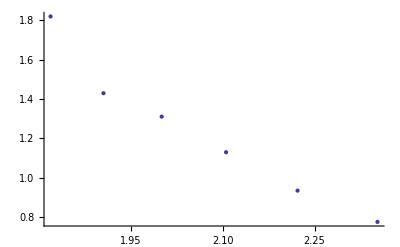

chi = 1

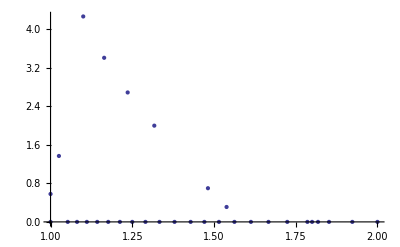

chi = 0.9

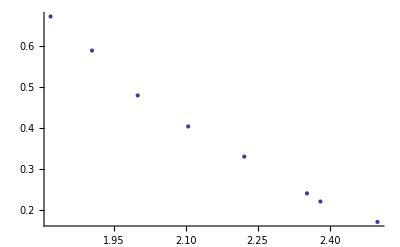

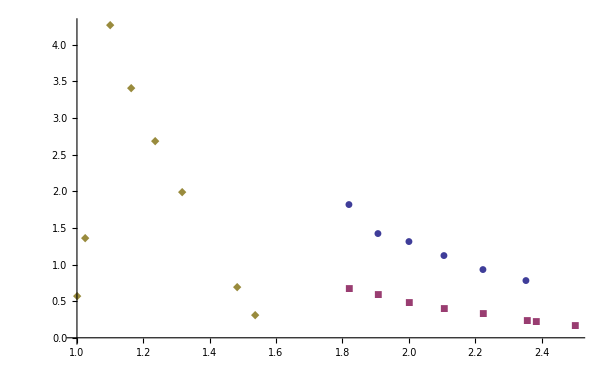

```mathematica
ListPlot[Select[#[[1,2,1]],Function[x,Last[x]≠0]]&/@{-Graphics-,-Graphics-,-Graphics-},PlotMarkers->Automatic,BaseStyle->{FontFamily->"Times",FontSize->12}]
```

```mathematica
1/.7
```

1.42857

```mathematica
Export["omega.eps",%110]
```

omega.eps

```mathematica
SetWorkDir[]
```

D:\programs\icmm\tormagn